```mathematica
(******* This notebook demonstrates the analysis of confidence composition for the mountain car (MC) case study *******)
```

```mathematica
(* import utility functions from composition-utils.nb *) 
NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"composition-utils.nb"]]];
```

```mathematica
(* loading the data *)
```

```mathematica
mgStepSize = 6; (* the parameter with which MG (mon2) was run - affects trace lengths *) 
resultsDir = NotebookDirectory[] <>  "mountaincar-logs/"; 
outcomeFiles = Select[FileNames[All,resultsDir],  StringTake[#,-7]== "out.csv"&];
mcFiles = Select[FileNames[All,resultsDir],  StringTake[#,-6]== "mc.csv"&];
mgFiles = Select[FileNames[All,resultsDir],  StringTake[#,-16]== "_mg_0.001500.csv"&];
```

```mathematica
successes = {}; stepCounts = {};  noiseAssnHolds = {}; steepAssnHolds = {}; allAssnHolds = {}; (*steeps = {};*) atLeastOneAssnHolds={};
With[{imp=Import@#},
AppendTo[successes, imp[[(*first line *) 1,(*1st element: success wrt the goal *) 1]]];
AppendTo[stepCounts, imp[[(*first line *) 1,(*2nd element: step count *) 2]]];
AppendTo[noiseAssnHolds, imp[[(*second line *) 2,(*2nd element: whether the noise assumptions hold *) 2]]];
(*AppendTo[steeps, imp[[(*second line *) 2,(*5th element: the steepness of the hill *) 5]]];*)
AppendTo[steepAssnHolds,imp[[(*second line *) 2,(*3rd element: steepness assn *) 3]]];
AppendTo[allAssnHolds,ToString[ToExpression@noiseAssnHolds[[-1]] ∧ ToExpression@steepAssnHolds[[-1]]]];
AppendTo[atLeastOneAssnHolds,ToString[ToExpression@noiseAssnHolds[[-1]] ∨ ToExpression@steepAssnHolds[[-1]]]];
]&/@ outcomeFiles;
(* monte carlo - mon1*)
mcProbs = Flatten[Import@# & /@ mcFiles, (*flatten at 3rd level*){3}][[1]];

(* mg (mon2) data *) 
mgCons = {}; mgRawConfs = {}; 
With[{imp = Import@#},
AppendTo[mgCons, imp[[(*all but first line *) 2;; ,(*2nd element: whether it was deemed consistent *) 2]]];
AppendTo[mgRawConfs, imp[[(*all but first line *) 2;; ,(*2nd element: whether it was deemed consistent *) 3]]];
]& /@ mgFiles;
(* transforming confidences to 1-rawconf when not consistent *) 
mgConfs = Table[ 
Table[
If[ mgCons[[i,j]] == 1, mgRawConfs[[i,j]], 1- mgRawConfs[[i,j]]]
, {j, 1, Length@mgCons[[i]]}]
, {i, 1, Length@mgCons}] ;
```

```mathematica
(** Organizing the data **)
```

```mathematica
(* assumption -> outcome pairs *) 
outNoiseAssnPairs = Inner[List, ToExpression/@successes,ToExpression/@noiseAssnHolds,  List]; 
outSteepAssnPairs = Inner[List, ToExpression/@successes,ToExpression/@steepAssnHolds,  List]; 
outAllAssnPairs = Inner[List, ToExpression/@successes,ToExpression/@allAssnHolds,  List]; 
outOneAssnHolds =  Inner[List, ToExpression/@successes,ToExpression/@atLeastOneAssnHolds,  List]; 
(* monitor -> outcome *) 
outMcPairs = fixExtremeProbs@Flatten[pairElemWithList/@ Inner[List,  successes,mcProbs, List] , {1,2}];
outMgPairs = fixExtremeProbs@ Flatten[pairElemWithList/@ Inner[List,  successes,mgConfs, List] , {1,2}];
(* monitor -> its assn *) 
noiseAssnMcPairs = fixExtremeProbs@Flatten[pairElemWithList/@ Inner[List,  noiseAssnHolds,mcProbs, List] , {1,2}];
steepAssnMgPairs = fixExtremeProbs@Flatten[pairElemWithList/@ Inner[List,  steepAssnHolds,mgConfs, List] , {1,2}];
(* monitor -> all assn *) 
allAssnMcPairs =  fixExtremeProbs@Flatten[pairElemWithList/@ Inner[List,  allAssnHolds,mcProbs, List] , {1,2}];
allAssnMgPairs = fixExtremeProbs@ Flatten[pairElemWithList/@ Inner[List,  allAssnHolds,mgConfs, List] , {1,2}];

(* Trimming the first N values of MC probs in each trace, to make composable with MG *) 
outMcPairsTr =fixExtremeProbs@ Flatten[pairElemWithList/@ Inner[List,  successes,mcProbs[[All,mgStepSize ;;]], List] , {1,2}];
noiseAssnMcPairsTr = fixExtremeProbs@Flatten[pairElemWithList/@ Inner[List,  noiseAssnHolds,mcProbs[[All,mgStepSize ;;]], List] , {1,2}];
allAssnMcPairsTr =  fixExtremeProbs@Flatten[pairElemWithList/@ Inner[List,  allAssnHolds,mcProbs[[All,mgStepSize ;;]], List] , {1,2}];
```

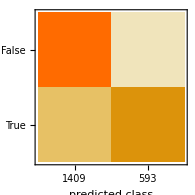
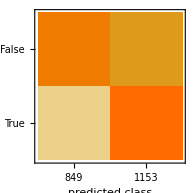
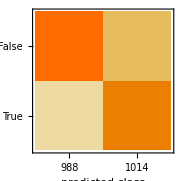
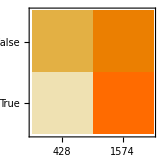

```mathematica
(** Evaluation of assumption-as-a-classifier-of-safety **) 
(* assumption "predictions" vs actual outcome *) 
{ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outAllAssnPairs), "ConfusionMatrixPlot"], ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outNoiseAssnPairs), "ConfusionMatrixPlot"], 
ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outSteepAssnPairs), "ConfusionMatrixPlot"],
(* at least one assumption true -> poor indicator of the outcome *) 
ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outOneAssnHolds), "ConfusionMatrixPlot"]}
```

```mathematica
{ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outAllAssnPairs), "Accuracy"], ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outNoiseAssnPairs), "Accuracy"], 
ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outSteepAssnPairs), "Accuracy"],
ClassifierMeasurements[assnClfer,(#-> outClfer[#]&/@ outOneAssnHolds), "Accuracy"]}
```

{0.851648,0.664835,0.796204,0.609391}

```mathematica
(* find verified runs that failed *) 
Pick[outcomeFiles,Nor[Not@#[[2]],#[[1]]]  &/@ outAllAssnPairs]
```

```mathematica
(** Calibratng monitors **)
```

```mathematica
(* mc to its assn *)
```

```mathematica
nll[noiseAssnMcPairsTr]
```

2029.64997135041616

```mathematica
(* with negative log likelihood *) 
Minimize[{nll[sigPairs[logOddsPairs[noiseAssnMcPairsTr], b]], b>=0}, b]
```

{1677.,{b→2.096}}

```mathematica
Minimize[nll[sigPairs[logOddsPairs[noiseAssnMcPairsTr], a, b]], {a,b}]
```

{1672.,{a→0.477,b→-0.1339}}

```mathematica
(* with brier score instead of nll *) 
Minimize[{brierScore[sigPairs[logOddsPairs[noiseAssnMcPairsTr], b]], b>=0}, b]
```

{0.05446,{b→1.688}}

```mathematica
Minimize[brierScore[sigPairs[logOddsPairs[noiseAssnMcPairsTr], a, b]], {a,b}]
```

{0.0544570237784,{a→0.591472465013,b→-0.0114580483611}}

```mathematica
(* saving various calibrations *) 
noiseAssnMcPairsTrCalTSNLL = sigPairs[logOddsPairs[noiseAssnMcPairsTr], 2.0956722845369980485`4.6104266844566055];
noiseAssnMcPairsTrCalPlaNLL =  sigPairs[logOddsPairs[noiseAssnMcPairsTr], 0.4769919790177934814`4.6104266844566055, 0.1338980618213111356`4.6104266844566055];
noiseAssnMcPairsTrCalTSBri =  sigPairs[logOddsPairs[noiseAssnMcPairsTr], 1.6878499701759968139`4.6104266844566055];
noiseAssnMcPairsTrCalPlaBri =  sigPairs[logOddsPairs[noiseAssnMcPairsTr],0.59147246501322052925562473092248528927`12.26921573653428, -0.01145804836111309370067888690882954969`12.26921573653428];

outMcPairsTrCalTSNLL = sigPairs[logOddsPairs[outMcPairsTr], 2.0956722845369980485`4.6104266844566055];
outMcPairsTrCalPlaNLL = sigPairs[logOddsPairs[outMcPairsTr],0.4769919790177934814`4.6104266844566055, 0.1338980618213111356`4.6104266844566055];
outMcPairsTrCalTSBri = sigPairs[logOddsPairs[outMcPairsTr], 1.6878499701759968139`4.6104266844566055];
outMcPairsTrCalPlaBri = sigPairs[logOddsPairs[outMcPairsTr], 0.59147246501322052925562473092248528927`12.26921573653428, -0.01145804836111309370067888690882954969`12.26921573653428];
```

```mathematica
(* mg to its assn, helps *)
```

```mathematica
nll[steepAssnMgPairs]
```

83892.3

```mathematica
(* with negative log likelihood *) 
Minimize[{nll[sigPairs[logOddsPairs[steepAssnMgPairs], b]], b≥(*FIXME*)5}, b]
```

{5484.42,{b→68.6004}}

```mathematica
Minimize[{nll[sigPairs[logOddsPairs[steepAssnMgPairs], a,b]], a>0, b>-10}, {a,b}]
```

{5358.15,{a→0.109827,b→0.346994}}

```mathematica
(* with brier score instead of nll *) 
Minimize[{brierScore[sigPairs[logOddsPairs[steepAssnMgPairs], b]], b>=0}, b]
```

{0.199536,{b→1.94005}}

```mathematica
Minimize[{brierScore[sigPairs[logOddsPairs[steepAssnMgPairs], a,b]], a>0, b>-10}, {a,b}]
```

{0.198126,{a→1.51899,b→-1.00294}}

```mathematica
(* the other calibrated monitors *) 
steepAssnMgPairsCalTSNLL = sigPairs[logOddsPairs[steepAssnMgPairs],68.60037345096815];
steepAssnMgPairsCalPlaNLL = sigPairs[logOddsPairs[steepAssnMgPairs],0.10982736131537235, 0.3469939310755595];
steepAssnMgPairsCalTSBri = sigPairs[logOddsPairs[steepAssnMgPairs],1.9400527978495328];
steepAssnMgPairsCalPlaBri = sigPairs[logOddsPairs[steepAssnMgPairs],1.5189862332841184,-1.0029372494801527];

outMgPairsCalTSNLL = sigPairs[logOddsPairs[outMgPairs],68.60037345096815];
outMgPairsCalPlaNLL = sigPairs[logOddsPairs[outMgPairs],0.10982736131537235, 0.3469939310755595];
outMgPairsCalTSBri = sigPairs[logOddsPairs[outMgPairs],1.9400527978495328];
outMgPairsCalPlaBri = sigPairs[logOddsPairs[outMgPairs],1.5189862332841184,-1.0029372494801527];
```

```mathematica
(* Logistic regression from uncalibrated monitors to conjunction of assumptions *) 
Clear[a,b,c];
triplesMcMg={ToString[ToExpression@#[[1,1]]∧ToExpression@#[[2,1]]], #[[1,2]], #[[2,2]]}&/@Transpose[{noiseAssnMcPairsTr, steepAssnMgPairs}]; 
pairsConjAssnMcMgLR ={#[[1]],sig[ a*Log[#[[2]]/(1-#[[2]])]+b*Log[#[[3]]/(1-#[[3]])]+c  ,1]}&/@triplesMcMg; 
Minimize[nll[pairsConjAssnMcMgLR],{a,b,c}]
```

{4546.01,{a→0.114094,b→0.0931994,c→-2.08638}}

```mathematica
conjAssnLrCompPairs = pairsConjAssnMcMgLR/.{a->0.11409410438776144,b->0.09319939368450716,c->-2.086377711941712}; 
outLrCompPairs = Transpose[{outMcPairsTr[[All,1]],(pairsConjAssnMcMgLR[[All,2]]/.{a->0.11409410438776144,b->0.09319939368450716,c->-2.086377711941712})}];
```

```mathematica
(* Logistic regression of calibrated monitors to conjunction of assumptions *) 
Clear[a,b,c];
triplesMcMg2={ToString[ToExpression@#[[1,1]]∧ToExpression@#[[2,1]]], #[[1,2]], #[[2,2]]}&/@Transpose[{noiseAssnMcPairsTrCalPlaNLL, steepAssnMgPairsCalPlaNLL}]; 
pairsConjAssnMcMgLR2 ={#[[1]],sig[ a*Log[#[[2]]/(1-#[[2]])]+b*Log[#[[3]]/(1-#[[3]])]+c  ,1]}&/@triplesMcMg2; 
Minimize[nll[pairsConjAssnMcMgLR2],{a,b,c}]
```

{4546.01,{a→0.2392,b→0.848733,c→-1.75997}}

```mathematica
conjAssnLrCompPairs2 = pairsConjAssnMcMgLR2/.{a->0.23920007244562685,b->0.8487326047416194,c->-1.759974211179954}; 
outLrCompPairs2 = Transpose[{outMcPairsTr[[All,1]],(pairsConjAssnMcMgLR2[[All,2]]/.{a->0.23920007244562685,b->0.8487326047416194,c->-1.759974211179954})}];
```

```mathematica
(* pairs organized by run *) 
pairsMcMg = Transpose/@(Transpose@{mcProbs[[All,mgStepSize ;;]], mgConfs});
pairsMcMgCal = Transpose/@(Transpose@{dynP[outMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs], 
dynP[outMgPairsCalPlaNLL[[All,2]], Length/@mgConfs]});

(* pick where assumptions hold*) 
mcProbsOnHolding = Flatten@Pick[
dynP[outMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs],  
#[[2]]&/@outAllAssnPairs
];
mgConfsOnHolding = Flatten@Pick[
dynP[outMgPairsCalPlaNLL[[All,2]], Length/@mgConfs],  
#[[2]]&/@outAllAssnPairs
];
(* density on assumptions holding *) 
jointSkdAssnSat= SmoothKernelDistribution[Transpose@{mcProbsOnHolding, mgConfsOnHolding}];
(* plotPDF3D@jointSkdAssnSat*)

(* pick where assumptions don't hold *) 
mcProbsOnNotHolding = Flatten@Pick[
dynP[outMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs],  
Not@#[[2]]&/@outAllAssnPairs
];
mgConfsOnNotHolding = Flatten@Pick[
dynP[outMgPairsCalPlaNLL[[All,2]], Length/@mgConfs],  
Not@#[[2]]&/@outAllAssnPairs
];
jointSkdAssnNotSat=   SmoothKernelDistribution[Transpose@{mcProbsOnNotHolding, mgConfsOnNotHolding}];
(*plotPDF3D@jointSkdAssnNotSat*)
Clear[bayesStep];
(* one step of bayesian inference *) 
bayesStep[ prior_, mcMg_]:= With[{mc=mcMg[[1]], mg=mcMg[[2]]},
prior*PDF[jointSkdAssnSat, {mc,mg}]/( 
PDF[jointSkdAssnSat, {mc,mg}] *prior +  PDF[jointSkdAssnNotSat, {mc,mg}] * (1-prior)
)];
applyBayesToRun[prior_,run_ ]:= Drop[FoldList[bayesStep , Join[{prior}, run]] ,1];
```

```mathematica
bayesCompResult = applyBayesToRun[0.5,#]& /@pairsMcMg; 
bayesCompCalResult = applyBayesToRun[0.5,#]& /@pairsMcMgCal;
```

```mathematica
(* putting bayes results together with the outcomes *) 
allAssnBayesPairs = Flatten[pairElemWithList/@ Inner[List,  allAssnHolds,bayesCompResult, List] , {1,2}];
outBayesPairs = Flatten[pairElemWithList/@ Inner[List,  successes,bayesCompResult, List] , {1,2}];
allAssnBayesCalPairs = Flatten[pairElemWithList/@ Inner[List,  allAssnHolds,bayesCompCalResult, List] , {1,2}];
outBayesCalPairs = Flatten[pairElemWithList/@ Inner[List,  successes,bayesCompCalResult, List] , {1,2}];
```

```mathematica
(** Composing monitors **) 

(* Product composition *) 
conjAssnIndAndCompPairs =composeMons[noiseAssnMcPairsTr,steepAssnMgPairs, And, Times];   
conjAssnIndAndCompPairsCalTSNLL =composeMons[noiseAssnMcPairsTrCalTSNLL, steepAssnMgPairsCalTSNLL, And, Times];   
conjAssnIndAndCompPairsCalTSBri =composeMons[noiseAssnMcPairsTrCalTSBri, steepAssnMgPairsCalTSBri, And, Times];   
conjAssnIndAndCompPairsCalPlaNLL =composeMons[noiseAssnMcPairsTrCalPlaNLL, steepAssnMgPairsCalPlaNLL, And, Times];   
conjAssnIndAndCompPairsCalPlaBri =composeMons[noiseAssnMcPairsTrCalPlaBri, steepAssnMgPairsCalPlaBri, And, Times];   

outIndAndCompPairs =composeMons[outMcPairsTr, outMgPairs,#1&, Times];   
outIndAndCompPairsCalTSNLL =composeMons[outMcPairsTrCalTSNLL, outMgPairsCalTSNLL,#1&, Times];   
outIndAndCompPairsCalTSBri = composeMons[outMcPairsTrCalTSBri, outMgPairsCalTSBri,#1&, Times];
outIndAndCompPairsCalPlaNLL = composeMons[outMcPairsTrCalPlaNLL, outMgPairsCalPlaNLL,#1&, Times];
outIndAndCompPairsCalPlaBri = composeMons[outMcPairsTrCalPlaBri, outMgPairsCalPlaBri,#1&, Times];

(* Averaging composition *) 
conjAssnAvgCompPairs =composeMons[noiseAssnMcPairsTr, steepAssnMgPairs,And, (#1+#2)/2&];
conjAssnAvgCompPairsCalTSNLL =composeMons[noiseAssnMcPairsTrCalTSNLL, steepAssnMgPairsCalTSNLL,And, (#1+#2)/2&];
conjAssnAvgCompPairsCalTSBri =composeMons[noiseAssnMcPairsTrCalTSBri, steepAssnMgPairsCalTSBri,And, (#1+#2)/2&];
conjAssnAvgCompPairsCalPlaNLL =composeMons[noiseAssnMcPairsTrCalPlaNLL, steepAssnMgPairsCalPlaNLL,And, (#1+#2)/2&];
conjAssnAvgCompPairsCalPlaBri =composeMons[noiseAssnMcPairsTrCalPlaBri, steepAssnMgPairsCalPlaBri,And, (#1+#2)/2&];

outAvgCompPairs =composeMons[outMcPairsTr, outMgPairs,#1&, (#1+#2)/2&];
outAvgCompPairsCalTSNLL =composeMons[outMcPairsTrCalTSNLL, outMgPairsCalTSNLL,#1&, (#1+#2)/2&];
outAvgCompPairsCalTSBri =composeMons[outMcPairsTrCalTSBri, outMgPairsCalTSBri,#1&, (#1+#2)/2&];
outAvgCompPairsCalPlaNLL =composeMons[outMcPairsTrCalPlaNLL, outMgPairsCalPlaNLL,#1&, (#1+#2)/2&];
outAvgCompPairsCalPlaBri =composeMons[outMcPairsTrCalPlaBri, outMgPairsCalPlaBri,#1&, (#1+#2)/2&];

(* Plus-minus 1 composition *) 
conjAssnPmoCompPairs =composeMons[noiseAssnMcPairsTr, steepAssnMgPairs,And, Max[#1+#2-1,0]&];
conjAssnPmoCompPairsCalTSNLL =composeMons[noiseAssnMcPairsTrCalTSNLL, steepAssnMgPairsCalTSNLL,And,  Max[#1+#2-1,0]&];
conjAssnPmoCompPairsCalTSBri =composeMons[noiseAssnMcPairsTrCalTSBri, steepAssnMgPairsCalTSBri,And,  Max[#1+#2-1,0]&];
conjAssnPmoCompPairsCalPlaNLL =composeMons[noiseAssnMcPairsTrCalPlaNLL, steepAssnMgPairsCalPlaNLL,And,  Max[#1+#2-1,0]&];
conjAssnPmoCompPairsCalPlaBri =composeMons[noiseAssnMcPairsTrCalPlaBri, steepAssnMgPairsCalPlaBri,And,  Max[#1+#2-1,0]&];

outPmoCompPairs =composeMons[outMcPairsTr, outMgPairs,#1&,  Max[#1+#2-1,0]&];
outPmoCompPairsCalTSNLL =composeMons[outMcPairsTrCalTSNLL, outMgPairsCalTSNLL,#1&,   Max[#1+#2-1,0]&];
outPmoCompPairsCalTSBri =composeMons[outMcPairsTrCalTSBri, outMgPairsCalTSBri,#1&, Max[#1+#2-1,0]&];
outPmoCompPairsCalPlaNLL =composeMons[outMcPairsTrCalPlaNLL, outMgPairsCalPlaNLL,#1&,  Max[#1+#2-1,0]&];
outPmoCompPairsCalPlaBri =composeMons[outMcPairsTrCalPlaBri, outMgPairsCalPlaBri,#1&,   Max[#1+#2-1,0]&];

(* Product-squared composition (following the guarantee) *) 
conjAssnProdSqCompPairs =composeMons[noiseAssnMcPairsTr, steepAssnMgPairs,And, Max[#1+#2-1,0]&];
conjAssnProdSqCompPairsCalTSNLL =composeMons[noiseAssnMcPairsTrCalTSNLL, steepAssnMgPairsCalTSNLL,And, (#1*#2)^2&];
conjAssnProdSqCompPairsCalTSBri =composeMons[noiseAssnMcPairsTrCalTSBri, steepAssnMgPairsCalTSBri,And, (#1*#2)^2&];
conjAssnProdSqCompPairsCalPlaNLL =composeMons[noiseAssnMcPairsTrCalPlaNLL, steepAssnMgPairsCalPlaNLL,And, (#1*#2)^2&];
conjAssnProdSqCompPairsCalPlaBri =composeMons[noiseAssnMcPairsTrCalPlaBri, steepAssnMgPairsCalPlaBri,And, (#1*#2)^2&];

outProdSqCompPairs =composeMons[outMcPairsTr, outMgPairs,#1&,  Max[#1+#2-1,0]&];
outProdSqCompPairsCalTSNLL =composeMons[outMcPairsTrCalTSNLL, outMgPairsCalTSNLL,#1&,  (#1*#2)^2&];
outProdSqCompPairsCalTSBri =composeMons[outMcPairsTrCalTSBri, outMgPairsCalTSBri,#1&, (#1*#2)^2&];
outProdSqCompPairsCalPlaNLL =composeMons[outMcPairsTrCalPlaNLL, outMgPairsCalPlaNLL,#1&,  (#1*#2)^2&];
outProdSqCompPairsCalPlaBri =composeMons[outMcPairsTrCalPlaBri, outMgPairsCalPlaBri,#1&, (#1*#2)^2&];

(* Independent-OR composition -- not useful *) 
(*disjAssnIndOrCompPairs =composeMons[noiseAssnMcPairsTr, steepAssnMgPairs,Or, (#1+#2-#1*#2)/2&];
outIndOrCompPairs = composeMons[noiseAssnMcPairsTr, steepAssnMgPairs,#1&, (#1+#2-#1*#2)/2&];*) 

(* Noisy-OR composition -- same as the product composition *)
```

```mathematica
(*** EVALUATION ***)
```

```mathematica
(* monitors-as-classifiers-of-safety *) 
classEval@noiseAssnMcPairs
classEval@outMcPairs
classEval@steepAssnMgPairs
classEval@outMgPairs
```

{0.939538,0.950139,0.941561,0.945831}

{0.641251,0.541029,0.743373,0.626262}

{0.725588,0.757459,0.649716,0.699463}

{0.64741,0.559123,0.585714,0.57211}

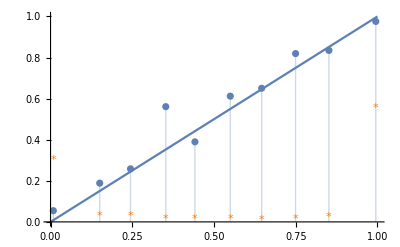
{0.0316964,-0.0519526,0.0198087,0.0489364,0.0559924660061479819,-Graphics-}

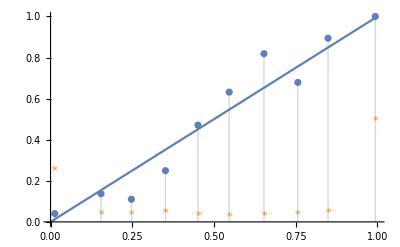
{0.0314438,-0.136875,0.0845788,0.0226744,0.0548,-Graphics-}

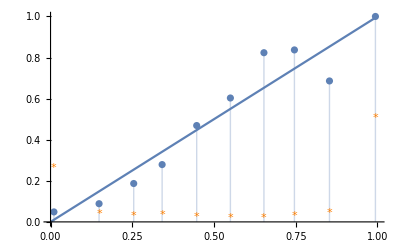
{0.0336875,-0.167133,0.0937156,0.0239166,0.05446,-Graphics-}

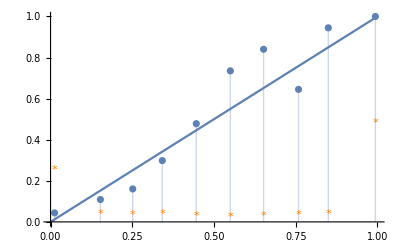
{0.0357624,-0.113457,0.0707211,0.029773,0.05504,-Graphics-}

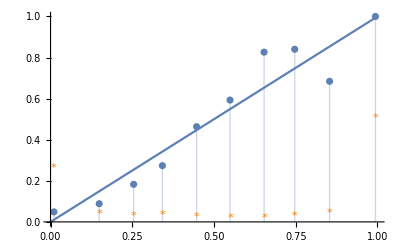
{0.0339956,-0.169287,0.0966686,0.0237765,0.0544570237784,-Graphics-}

```mathematica
(** Monitor calibration evaluation *) 
(* mon->its assn calibration eval, this is what we try to do *)
calibEval@noiseAssnMcPairsTr
calibEval@noiseAssnMcPairsTrCalTSNLL
calibEval@noiseAssnMcPairsTrCalTSBri
calibEval@noiseAssnMcPairsTrCalPlaNLL
calibEval@noiseAssnMcPairsTrCalPlaBri
```

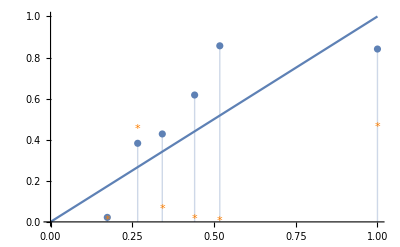
{0.135465,-0.158528,0.158389,0.115093,0.205272,-Graphics-}

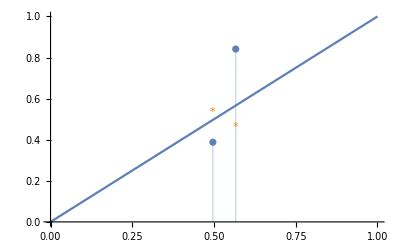
{0.185816,-0.108747,0.108747,0.275132,0.230572,-Graphics-}

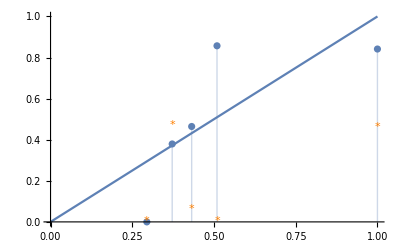
{0.0800973,-0.294546,0.159221,0.0117075,0.199525,-Graphics-}

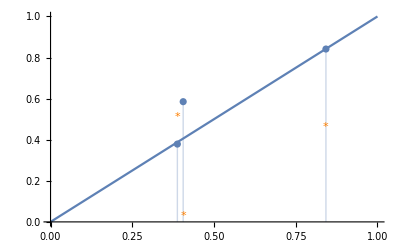
{0.0101456,-0.0091058,0.00522038,0.179446,0.189241,-Graphics-}

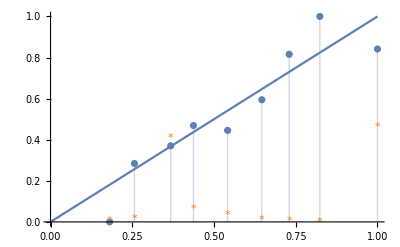
{0.0814062,-0.180835,0.152399,0.00782483,0.198126,-Graphics-}

```mathematica
calibEval@steepAssnMgPairs
calibEval@steepAssnMgPairsCalTSNLL
calibEval@steepAssnMgPairsCalTSBri
calibEval@steepAssnMgPairsCalPlaNLL
calibEval@steepAssnMgPairsCalPlaBri
```

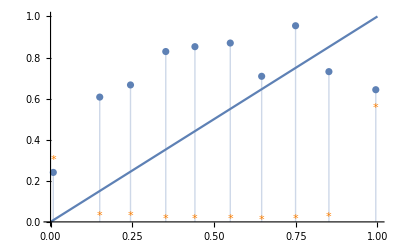
{0.311339,-0.351441,0.341293,0.270374,0.309689503173198714,-Graphics-}

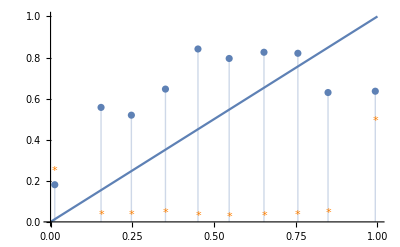
{0.283802,-0.35727,0.346441,0.213048,0.29155,-Graphics-}

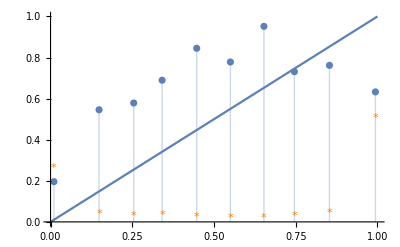
{0.29125,-0.36092,0.325007,0.245221,0.29706,-Graphics-}

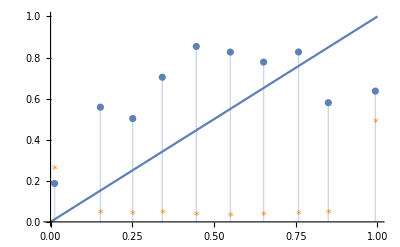
{0.28932,-0.356926,0.350575,0.22264,0.29449,-Graphics-}

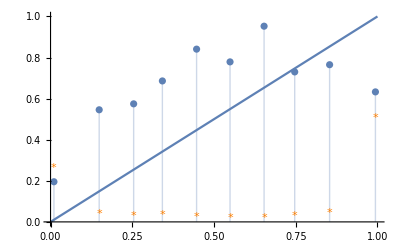
{0.290791,-0.360974,0.324976,0.244139,0.2967847418744,-Graphics-}

```mathematica
(* mon->outcome calibration eval, not particularly insightful *)
calibEval@outMcPairsTr
calibEval@outMcPairsTrCalTSNLL
calibEval@outMcPairsTrCalTSBri
calibEval@outMcPairsTrCalPlaNLL
calibEval@outMcPairsTrCalPlaBri
```

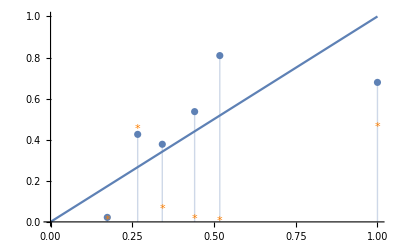
{0.225508,-0.320918,0.31749,0.143766,0.288809,-Graphics-}

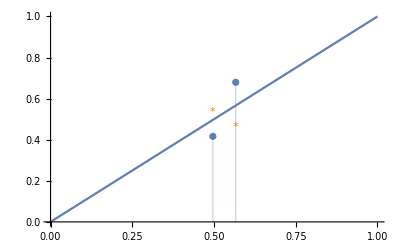
{0.0955637,-0.0802703,0.0802703,0.113287,0.240703,-Graphics-}

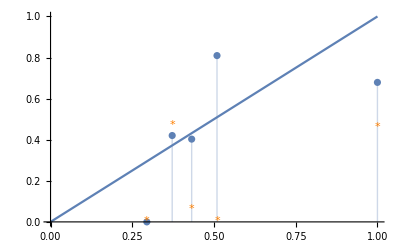
{0.173863,-0.320842,0.284941,0.0494466,0.279181,-Graphics-}

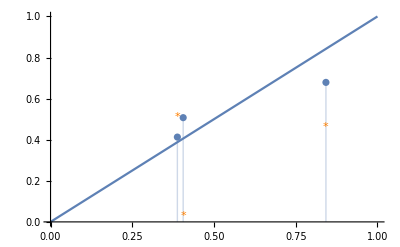
{0.0908873,-0.163305,0.163305,0.0289495,0.244122,-Graphics-}

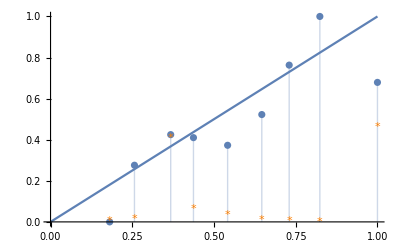
{0.181199,-0.320918,0.274506,0.0559727,0.279705,-Graphics-}

```mathematica
calibEval@outMgPairs
calibEval@outMgPairsCalTSNLL
calibEval@outMgPairsCalTSBri
calibEval@outMgPairsCalPlaNLL
calibEval@outMgPairsCalPlaBri
```

```mathematica
(** Composition calibration evaluation **)
```

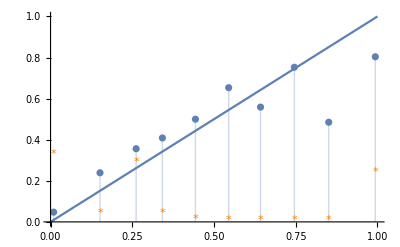
{0.099121,-0.365808,0.193832,0.0655766,0.161901,-Graphics-}

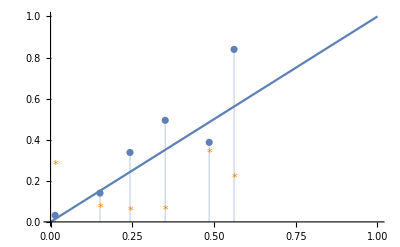
{0.110796,-0.0982539,0.0833739,0.129282,0.172003,-Graphics-}

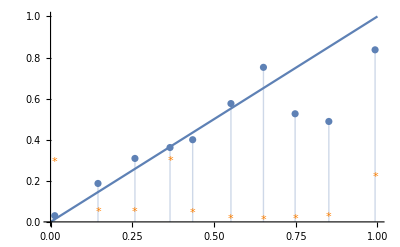
{0.0583724,-0.362384,0.0805703,0.0263888,0.156007,-Graphics-}

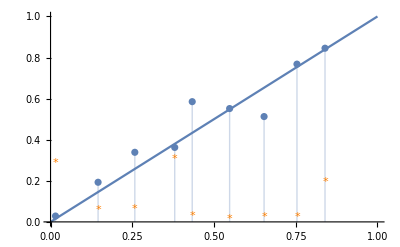
{0.026214,-0.140455,0.0265657,0.026041,0.149615,-Graphics-}

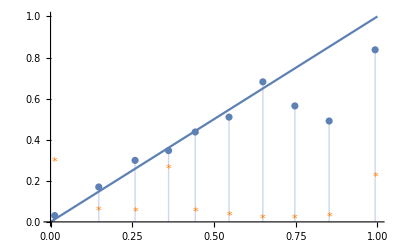
{0.058784,-0.361034,0.0842261,0.0219031,0.154891,-Graphics-}

```mathematica
(* independent-AND/multiplicative - improves after calibration but still not as good as averaging *) 

(* prediction of assumption conjunction *) 
calibEval@conjAssnIndAndCompPairs 
calibEval@conjAssnIndAndCompPairsCalTSNLL
calibEval@conjAssnIndAndCompPairsCalTSBri
calibEval@conjAssnIndAndCompPairsCalPlaNLL
calibEval@conjAssnIndAndCompPairsCalPlaBri
```

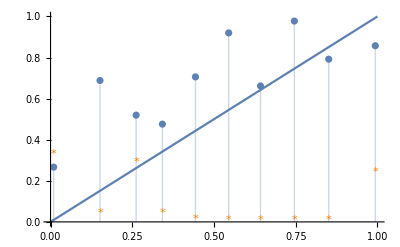
{0.231531,-0.135924,0.132722,0.265248,0.254065,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

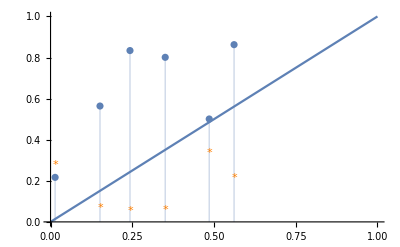
{0.209915,0.0155392,Indeterminate,0.209915,0.259951,-Graphics-}

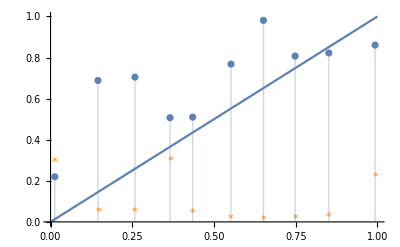
{0.188642,-0.132162,0.122127,0.209886,0.23452,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

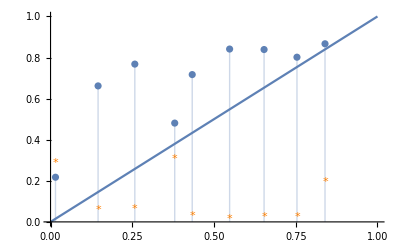
{0.174962,0.0274099,Indeterminate,0.174962,0.236736,-Graphics-}

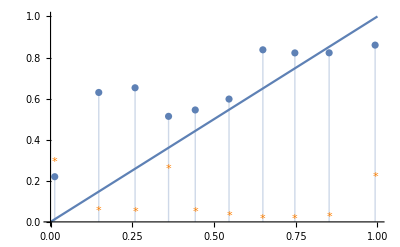
{0.184554,-0.132279,0.122205,0.204478,0.233003,-Graphics-}

```mathematica
(* predictions of outcome *) 
calibEval@outIndAndCompPairs 
calibEval@outIndAndCompPairsCalTSNLL
calibEval@outIndAndCompPairsCalTSBri
calibEval@outIndAndCompPairsCalPlaNLL
calibEval@outIndAndCompPairsCalPlaBri
```

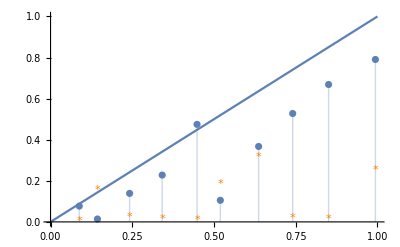
{0.244923,-0.414247,0.24721,0.0265897,0.219243,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

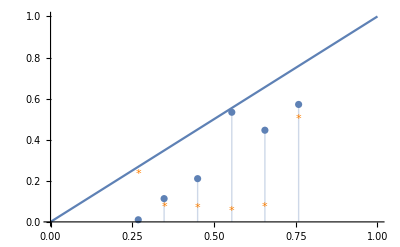
{0.20343,-0.25795,0.20343,Indeterminate,0.215535,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

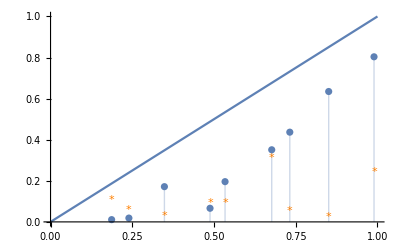
{0.271747,-0.42151,0.271747,Indeterminate,0.232451,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

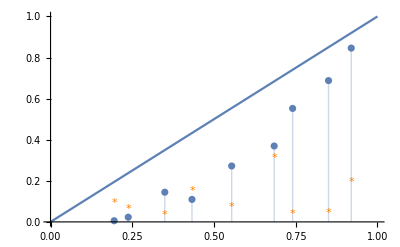
{0.234165,-0.323153,0.234165,Indeterminate,0.214909,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

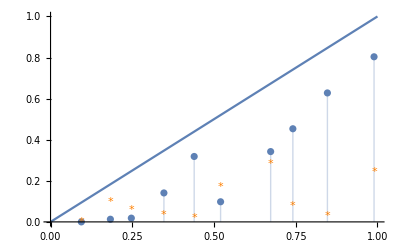
{0.275118,-0.422166,0.275118,Indeterminate,0.233457,-Graphics-}

```mathematica
(* Averaging composition 
- does not improve after calibration *) 

(* predicting the assumption conjunction 
- poorly as expected *) 
calibEval@conjAssnAvgCompPairs 
calibEval@conjAssnAvgCompPairsCalTSNLL
calibEval@conjAssnAvgCompPairsCalTSBri
calibEval@conjAssnAvgCompPairsCalPlaNLL
calibEval@conjAssnAvgCompPairsCalPlaBri
```

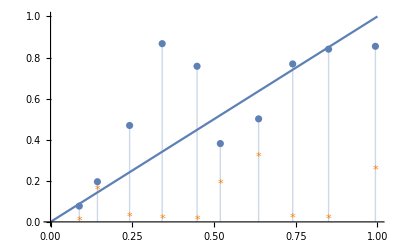
{0.128711,-0.138995,0.133938,0.111007,0.213024,-Graphics-}

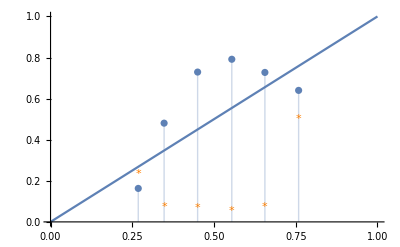
{0.130778,-0.118691,0.114474,0.175659,0.218753,-Graphics-}

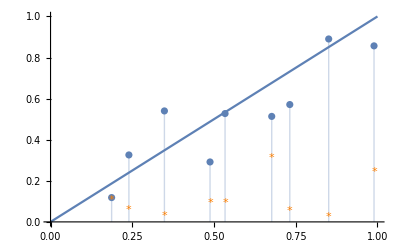
{0.127997,-0.196109,0.13085,0.104394,0.214439,-Graphics-}

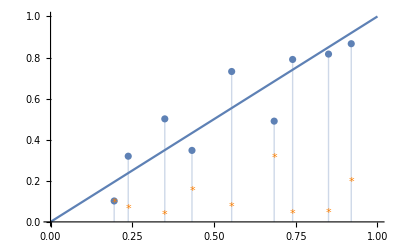
{0.118867,-0.193601,0.118024,0.122061,0.209362,-Graphics-}

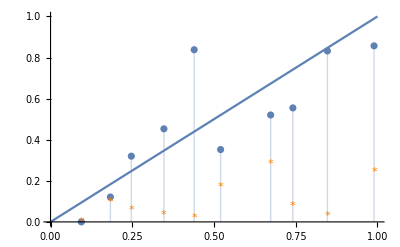
{0.138761,-0.186281,0.138675,0.139482,0.214659,-Graphics-}

```mathematica
(* predicting the outcome 
- does surprisingly well *) 


calibEval@outAvgCompPairs 
calibEval@outAvgCompPairsCalTSNLL
calibEval@outAvgCompPairsCalTSBri
calibEval@outAvgCompPairsCalPlaNLL
calibEval@outAvgCompPairsCalPlaBri
```

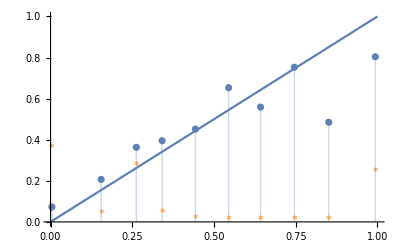
{0.10772,-0.365808,0.193832,0.0772213,0.165799,-Graphics-}

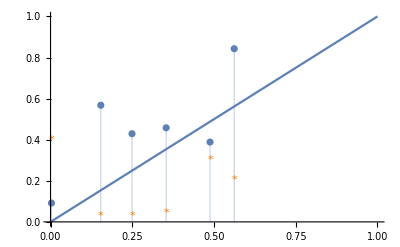
{0.143889,-0.0992433,0.0992433,0.162982,0.184696,-Graphics-}

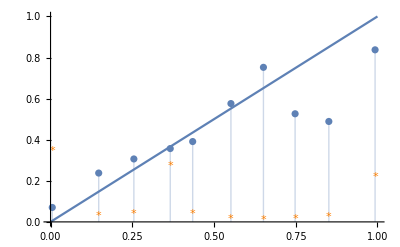
{0.0776177,-0.362373,0.0870301,0.0652946,0.161042,-Graphics-}

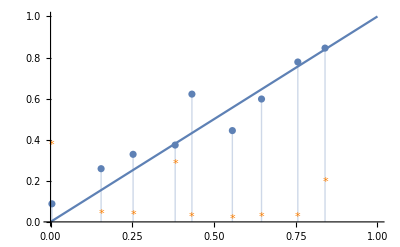
{0.0485192,-0.111707,0.0146697,0.064293,0.157559,-Graphics-}

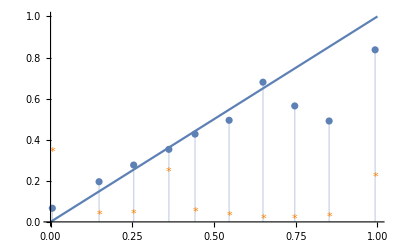
{0.0728543,-0.361034,0.0860311,0.0553055,0.159162,-Graphics-}

```mathematica
(* Plus-minus one composition 
- *) 

(* predicting the assumption conjunction 
- does surprisingly well *) 
calibEval@conjAssnPmoCompPairs 
calibEval@conjAssnPmoCompPairsCalTSNLL
calibEval@conjAssnPmoCompPairsCalTSBri
calibEval@conjAssnPmoCompPairsCalPlaNLL
calibEval@conjAssnPmoCompPairsCalPlaBri
```

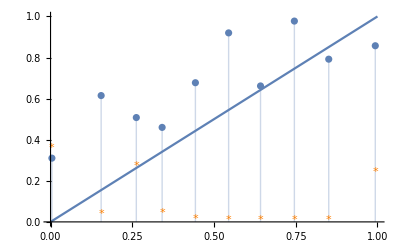
{0.24013,-0.135924,0.132722,0.276782,0.264475,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

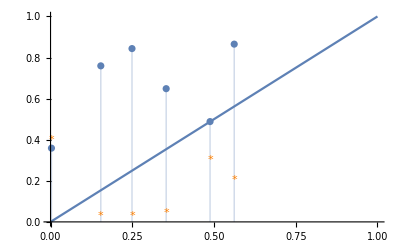
{0.250698,0.000372206,Indeterminate,0.250698,0.302458,-Graphics-}

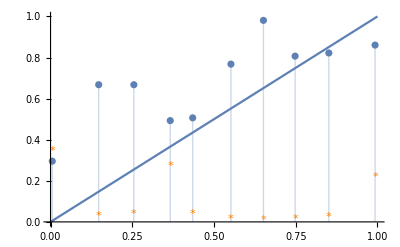
{0.204324,-0.132161,0.122125,0.230577,0.250809,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

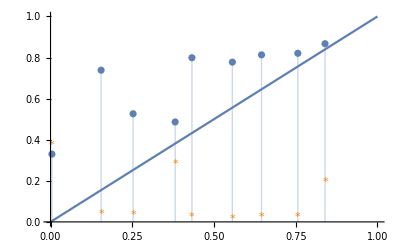
{0.205458,0.0277223,Indeterminate,0.205458,0.266361,-Graphics-}

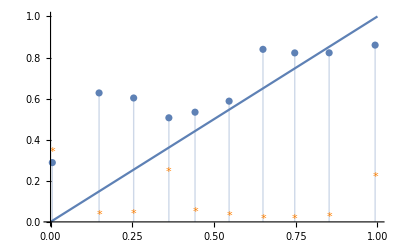
{0.200037,-0.132279,0.122205,0.224909,0.248542,-Graphics-}

```mathematica
(* predicting the outcome 
- okish *) 
calibEval@outPmoCompPairs 
calibEval@outPmoCompPairsCalTSNLL
calibEval@outPmoCompPairsCalTSBri
calibEval@outPmoCompPairsCalPlaNLL
calibEval@outPmoCompPairsCalPlaBri
```

```mathematica
(* Product-squared composition*)
```

```mathematica
(* predicting the conjunction*)
```

{0.10772,-0.365808,0.193832,0.0772213,0.165799,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

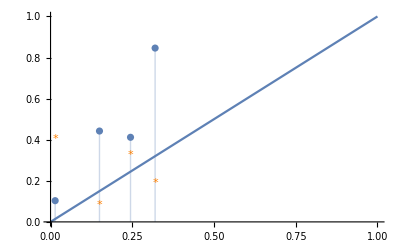
{0.214041,0.0891703,Indeterminate,0.214041,0.230097,-Graphics-}

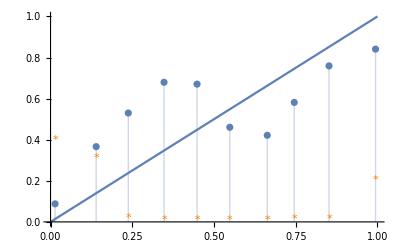
{0.149276,-0.241383,0.152036,0.148342,0.176622,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

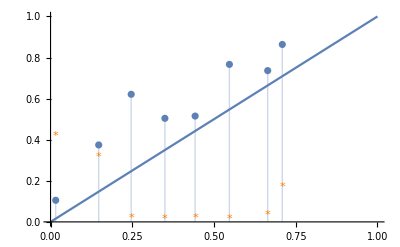
{0.150643,0.0720765,Indeterminate,0.150643,0.179383,-Graphics-}

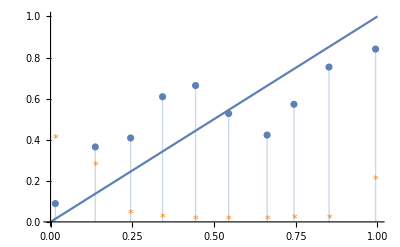
{0.144203,-0.23974,0.14959,0.142363,0.17374,-Graphics-}

```mathematica
calibEval@conjAssnProdSqCompPairs 
calibEval@conjAssnProdSqCompPairsCalTSNLL
calibEval@conjAssnProdSqCompPairsCalTSBri
calibEval@conjAssnProdSqCompPairsCalPlaNLL
calibEval@conjAssnProdSqCompPairsCalPlaBri
```

```mathematica
(* predicting the outcome*)
```

{0.24013,-0.135924,0.132722,0.276782,0.264475,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

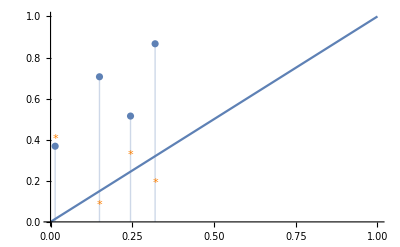
{0.380307,0.270549,Indeterminate,0.380307,0.366523,-Graphics-}

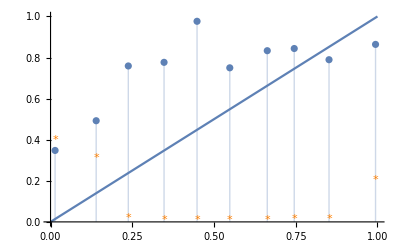
{0.29389,-0.130146,0.125845,0.341136,0.298085,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

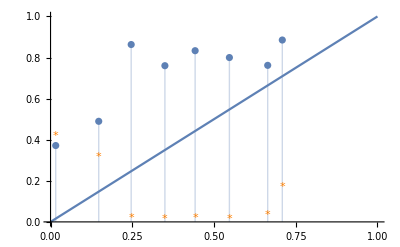
{0.316909,0.0978,Indeterminate,0.316909,0.312475,-Graphics-}

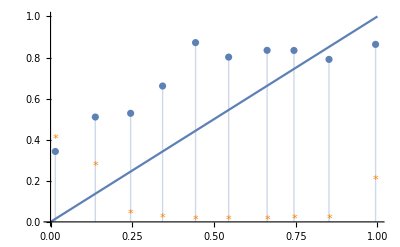
{0.289571,-0.130206,0.125768,0.335682,0.29502,-Graphics-}

```mathematica
calibEval@outProdSqCompPairs 
calibEval@outProdSqCompPairsCalTSNLL
calibEval@outProdSqCompPairsCalTSBri
calibEval@outProdSqCompPairsCalPlaNLL
calibEval@outProdSqCompPairsCalPlaBri
```

```mathematica
(* LogReg composition 
-- does with predicting assumption conjunction
-- so-so with predicting outcome *)
```

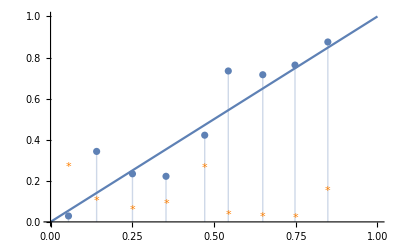
{0.0647869,-0.13124,0.0479805,0.0997104,0.158129,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

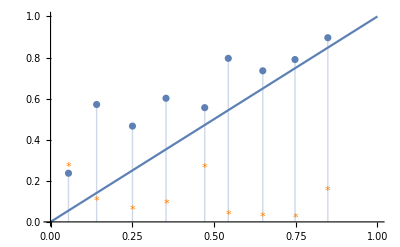
{0.166268,0.0425866,Indeterminate,0.166268,0.238996,-Graphics-}

```mathematica
calibEval@conjAssnLrCompPairs
calibEval@outLrCompPairs
```

```mathematica
(* LogReg composition on calibrated monitors 
-- does with predicting assumption conjunction
-- so-so with predicting outcome *)
```

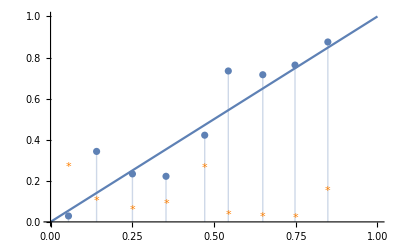
{0.0648,-0.131252,0.047992,0.0997268,0.158128,-Graphics-}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

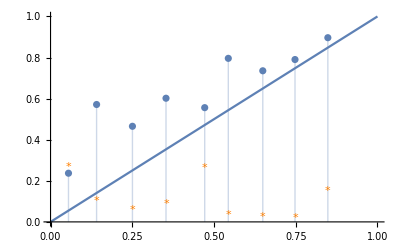
{0.166265,0.0425545,Indeterminate,0.166265,0.238993,-Graphics-}

```mathematica
calibEval@conjAssnLrCompPairs2
calibEval@outLrCompPairs2
```

```mathematica
(* Bayes composition uncalibrated
- on assumptions and outcome *)
```

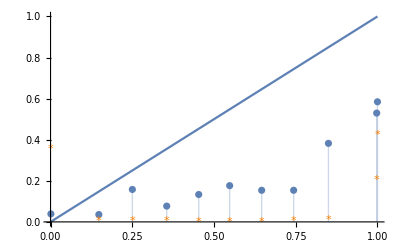
{0.291399,-0.589771,0.430055,0.0379844,Indeterminate,-Graphics-}

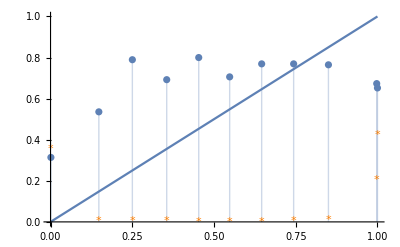
{0.327848,-0.347999,0.337479,0.31136,Indeterminate,-Graphics-}

```mathematica
calibEval@allAssnBayesPairs 
calibEval@outBayesPairs
```

General::munfl: (-2.48277×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.75193×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.94423×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

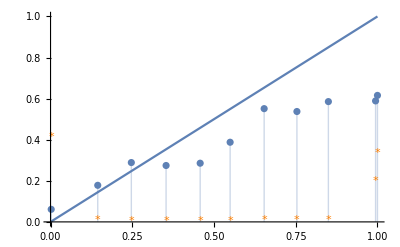
{0.242169,-0.405261,0.37696,0.0584576,0.248475,-Graphics-}

General::munfl: (-2.48277×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.75193×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.94423×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

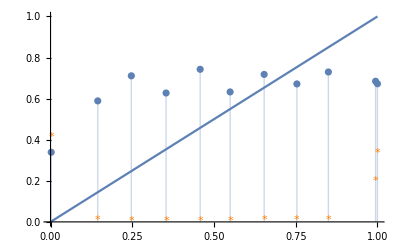
{0.321338,-0.327597,0.313584,0.330989,0.325611,-Graphics-}

```mathematica
(* Bayes composition calibrated
- on assumptions and outcome *) 
calibEval@allAssnBayesCalPairs
calibEval@outBayesCalPairs
```

```mathematica
(** ROC/AUC evaluation **)
```

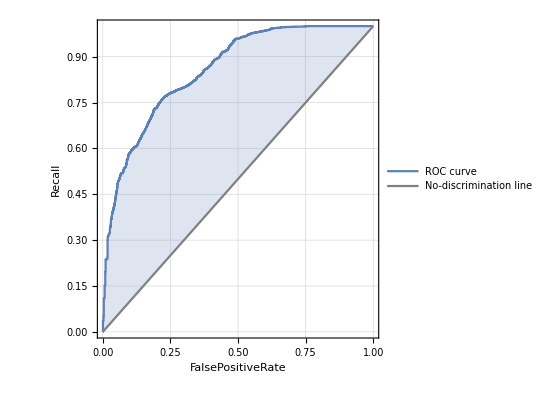
{-Graphics-,0.856212}

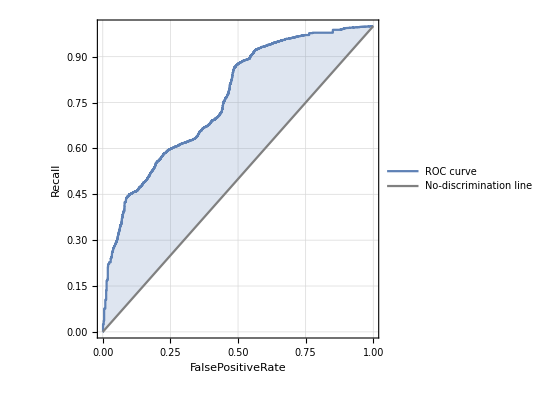
{-Graphics-,0.75925}

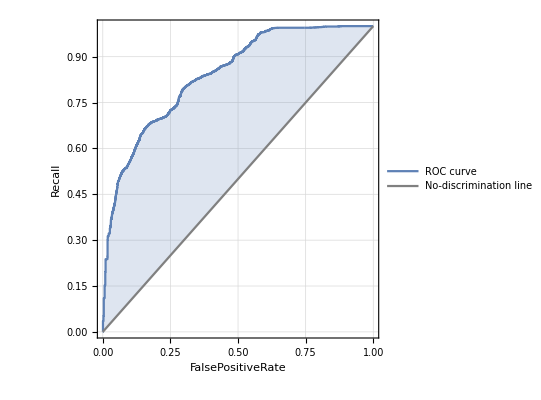
{-Graphics-,0.841308}

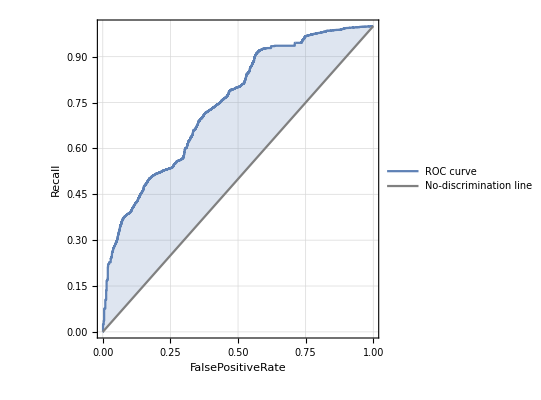
{-Graphics-,0.746297}

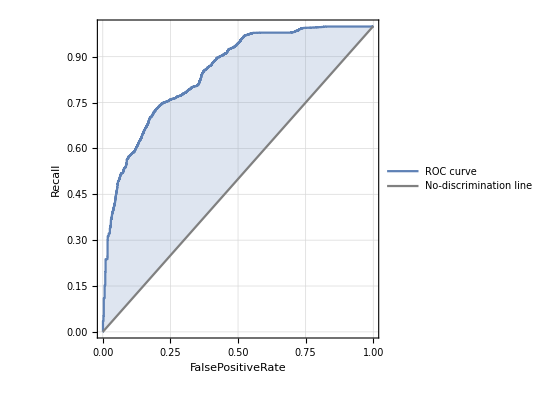
{-Graphics-,0.849114}

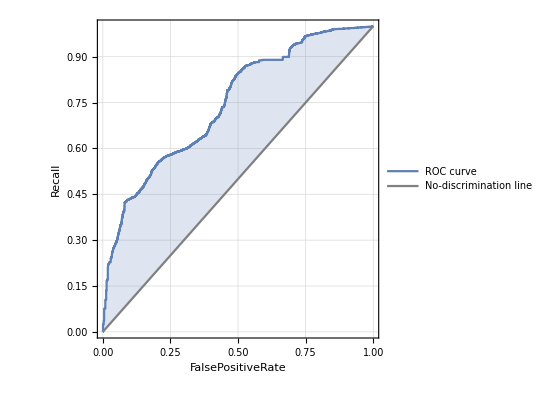
{-Graphics-,0.744321}

```mathematica
{roc[conjAssnIndAndCompPairsCalPlaNLL],auc[conjAssnIndAndCompPairsCalPlaNLL]}
{roc[outIndAndCompPairsCalPlaNLL], auc[outIndAndCompPairsCalPlaNLL]}
{roc[conjAssnLrCompPairs], auc[conjAssnLrCompPairs]}
{roc[outLrCompPairs],auc[outLrCompPairs]}
{roc[conjAssnAvgCompPairsCalPlaNLL], auc[conjAssnAvgCompPairsCalPlaNLL]}
{roc[outAvgCompPairsCalPlaNLL],auc[outAvgCompPairsCalPlaNLL]}
```

```mathematica
(*** VISUALIZATION OF RUNS ***)
```

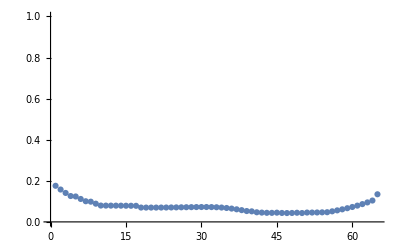
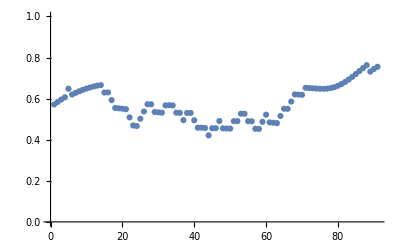
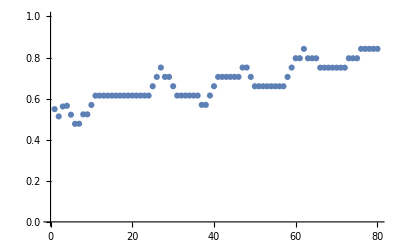
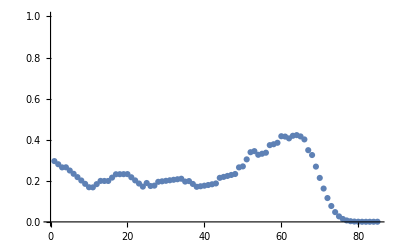
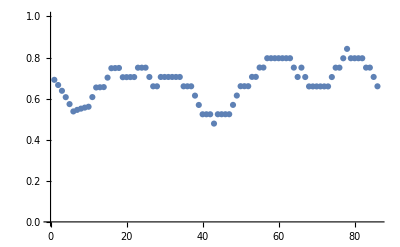
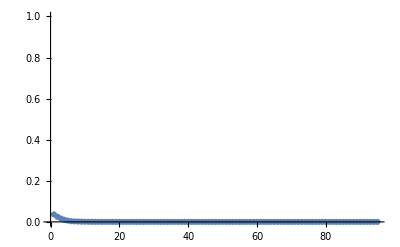
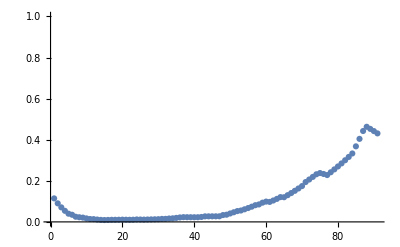
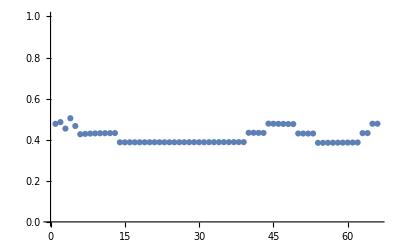
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* successful runs *) 
ListPlot[#, PlotRange->{0,1}]&/@Pick[
MovingAverage[#,10]&/@ dynP[conjAssnIndAndCompPairsCalPlaNLL[[All,2]], Length/@mgConfs],
 ToExpression/@successes]
```

```mathematica
(* successful runs with assns holding, with calibration *) 
ListPlot[#, PlotRange->{0,1}]&/@Pick[
Transpose@{MovingAverage[#,10]&/@dynP[conjAssnIndAndCompPairsCalPlaNLL[[All,2]], Length/@mgConfs], 
MovingAverage[#,10]&/@dynP[outAvgCompPairsCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[noiseAssnMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[steepAssnMgPairsCalPlaNLL[[All,2]], Length/@mgConfs]
},
And@@#&/@outAllAssnPairs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* successful runs with assns holding, with calibration *) 
succPlt=(ListPlot[#, PlotRange->{0,1},  Joined->{True, True, True, True},InterpolationOrder->2,  PlotStyle->{ Dotted, Dotted, AbsoluteDashing[0], AbsoluteDashing[0]}, PlotLegends->{ "M_1", "M_2","M_1*M_2", "(M_1+M_2)/2"}]&/@
Pick[
Transpose@{
MovingAverage[#,10]&/@dynP[noiseAssnMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[steepAssnMgPairsCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[conjAssnIndAndCompPairsCalPlaNLL[[All,2]], Length/@mgConfs], 
MovingAverage[#,10]&/@dynP[outAvgCompPairsCalPlaNLL[[All,2]], Length/@mgConfs]
},
And@@#&/@outAllAssnPairs])[[4(*,21*)]]
Export["~/succPlt.svg", succPlt];
Export["~/succPlt.pdf", succPlt];
Export["~/succPlt.png", succPlt];
```

-Graphics-

```mathematica
(* failed runs with assns not holding, with calibration *) 
ListPlot[#, PlotRange->{0,1}]&/@Pick[
Transpose@{MovingAverage[#,10]&/@dynP[conjAssnIndAndCompPairsCalPlaNLL[[All,2]], Length/@mgConfs], 
MovingAverage[#,10]&/@dynP[outAvgCompPairsCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[noiseAssnMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[steepAssnMgPairsCalPlaNLL[[All,2]], Length/@mgConfs]
},
Nor@@#&/@outAllAssnPairs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* failed runs of interest *) 
failPlt=(ListPlot[#, PlotRange->{0,1}, Joined->{True, True, True, True},InterpolationOrder->2,
PlotStyle->{ Dotted, Dotted, AbsoluteDashing[0], AbsoluteDashing[0]}, PlotLegends->{ "M_1", "M_2","M_1*M_2", "(M_1+M_2)/2"}]&/@Pick[
Transpose@{
MovingAverage[#,10]&/@dynP[noiseAssnMcPairsTrCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[steepAssnMgPairsCalPlaNLL[[All,2]], Length/@mgConfs],
MovingAverage[#,10]&/@dynP[conjAssnIndAndCompPairsCalPlaNLL[[All,2]], Length/@mgConfs], 
MovingAverage[#,10]&/@dynP[outAvgCompPairsCalPlaNLL[[All,2]], Length/@mgConfs]
},
Nor@@#&/@outAllAssnPairs])[[23]]
Export["~/failPlt.svg", failPlt];
Export["~/failPlt.pdf", failPlt];
Export["~/failPlt.png", failPlt];
```

-Graphics-

```mathematica
(*** Running automated validation and testing of monitors ***)
```

```mathematica
(*another round, with fixed bayes *) 
addHeadingsToResultsMatrix@Mean[doMcEvals[resultsDir, 1, 0.5]]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b} = {2.2116,1.00612}.

General::munfl: (-5.29416×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.11759×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.24468×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.0774456 | 0.215011 | -0.215011 | 0.12856 | 0.886498
Prod-outcome | 0.122941 | 0.302754 | -0.18726 | 0.2025 | 0.786254
Avg-assn | 0.325353 | 0.46304 | -0.46304 | 0.23697 | 0.877354
Avg-outcome | 0.209098 | 0.308717 | -0.308717 | 0.23047 | 0.76862
AvgVar-assn | 0.341912 | 0.631814 | -0.631814 | 0.25918 | 0.808755
AvgVar-outcome | 0.219158 | 0.456474 | -0.456474 | 0.23992 | 0.742751
LowCop-assn | 0.0846619 | 0.215005 | -0.215005 | 0.13053 | 0.548231
LowCop-outcome | 0.144747 | 0.320821 | -0.18726 | 0.21471 | 0.525508
ProdSq-assn | 0.0966963 | 0.209145 | -0.209145 | 0.13195 | 0.886498
ProdSq-outcome | 0.21975 | 0.431609 | -0.183042 | 0.23679 | 0.786254
LR-assn | 0.0534854 | 0.289945 | -0.111258 | 0.12989 | 0.864887
LR-outcome | 0.128348 | 0.331028 | 0.0157119 | 0.21223 | 0.763011
Bayes-assn | 0.255617 | 0.582162 | -0.582162 | 0.25517 | 0.905917
Bayes-outcome | 0.303976 | 0.496145 | -0.496145 | 0.3096 | 0.777347)

```mathematica
(* manual testing of the bayesian estimator *)
```

```mathematica
Length@outcomeFiles
```

2002

```mathematica
(*validation*) 
loadAndOrganizeMcData[resultsDir, Range[1000]];
```

```mathematica
jointSkdAssnSat= SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,ToExpression@a1AndA2Holds],  Flatten@Pick[m2sByRun,ToExpression@a1AndA2Holds]}
];
```

```mathematica
jointSkdAssnNotSat= SmoothKernelDistribution[Transpose@{Flatten@ Pick[m1sByRun,Not/@ToExpression@a1AndA2Holds],  Flatten@Pick[m2sByRun,Not/@ToExpression@a1AndA2Holds]}
];
```

```mathematica
{plotPDF3D@jointSkdAssnSat, plotPDF3D@jointSkdAssnNotSat}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
ListPlot@Transpose@{ Flatten@Pick[m1sByRun,ToExpression@a1AndA2Holds],  Flatten@Pick[m2sByRun,ToExpression@a1AndA2Holds]}
```

-Graphics-

```mathematica
(*both true *) 
Histogram3D[Transpose@{ Flatten@Pick[m1sByRun,ToExpression@a1AndA2Holds],  Flatten@Pick[m2sByRun,ToExpression@a1AndA2Holds]},Automatic, "Probability"]
```

-Graphics3D-

```mathematica
Histogram3D[Transpose@{ Flatten@Pick[m1sByRun,firstTsecondF],  Flatten@Pick[m2sByRun,firstTsecondF]},Automatic, "Probability"]
```

-Graphics3D-

```mathematica
plotPDF3D@SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstTsecondF],  Flatten@Pick[m2sByRun,firstTsecondF]}]
```

-Graphics3D-

```mathematica
Histogram3D[Transpose@{ Flatten@Pick[m1sByRun,firstFsecondT],  Flatten@Pick[m2sByRun,firstFsecondT]},Automatic, "Probability"]
```

-Graphics3D-

```mathematica
plotPDF3D@SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstFsecondT],  Flatten@Pick[m2sByRun,firstFsecondT]}]
```

-Graphics3D-

```mathematica
Histogram3D@Transpose@{ Flatten@Pick[m1sByRun,firstFsecondF],  Flatten@Pick[m2sByRun,firstFsecondF]}
```

-Graphics3D-

```mathematica
hnew = (h[[2]]+10^-5)/Plus@@(Flatten@(h[[2]]+10^-5))
```

{{9.95183×10^-6,9.95183×10^-6,0.000100853,0.004555,0.0316889,0.522236,0.0102363,0.00414594,0.00346419,0.00255518,0.000509907,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.176858,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00319148,0.024735,0.000691709,0.000146303,0.000146303,0.000146303,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.0096,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00123711,0.0174629,0.000419006,0.0000554023,0.000100853,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00505495,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00105531,0.0151904,0.000282655,0.0000554023,0.000237204,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.004555,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00078261,0.0177356,0.000509907,9.95183×10^-6,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00832739,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000555357,0.0123725,0.0000554023,9.95183×10^-6,9.95183×10^-6,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00505495,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000555357,0.00814558,0.000237204,0.000100853,0.000100853,0.0000554023,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00355509,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00082806,0.00964545,0.000282655,0.000100853,0.000100853,9.95183×10^-6,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00332784,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000964412,0.0097818,9.95183×10^-6,9.95183×10^-6,0.0000554023,9.95183×10^-6,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00387324,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000464456,0.0092364,0.000146303,0.000100853,0.000100853,0.000146303,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00214612,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000100853,0.000373556,0.00700932,0.000237204,9.95183×10^-6,0.000100853,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00205522,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000282655,0.000646258,0.00505495,0.000237204,0.000146303,9.95183×10^-6,0.000100853,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00160072,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000419006,0.00341874,0.000146303,0.0000554023,0.000100853,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000964412,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000282655,0.00300968,0.000191754,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000964412,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000191754,0.0042823,0.000100853,0.000191754,0.000191754,0.000146303,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.00110076,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000146303,0.00082806,0.00287333,0.000146303,0.000237204,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000555357,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000146303,0.000146303,0.00255518,0.000191754,0.000100853,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000464456,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.0000554023,0.000373556,0.00300968,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000464456,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000146303,0.000873511,0.00173707,0.0000554023,0.0000554023,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.0000554023,0.00155527,0.00337329,0.000600808,0.000373556,0.000464456,0.000100853,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,0.000373556,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6},{9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6,9.95183×10^-6}}

```mathematica
h[[1]], h[[2]]+10^-5/Plus@@(Flatten@(h[[2]]+10^-5))
```

```mathematica
h = HistogramList[Transpose@{ Flatten@Pick[m1sByRun,firstFsecondF],  Flatten@Pick[m2sByRun,firstFsecondF]}, {{0,1.1,0.05},{0,1.1,0.05}},"Probability"]
```

{{{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1},{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1}},{{0.,0.,0.0000913409,0.00456704,0.0318323,0.524753,0.0102758,0.00415601,0.00347095,0.00255754,0.000502375,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.177704,0.},{0.,0.,0.,0.,0.00319693,0.0248447,0.000685057,0.000137011,0.000137011,0.000137011,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00963646,0.},{0.,0.,0.,0.,0.0012331,0.0175374,0.000411034,0.0000456704,0.0000913409,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00506942,0.},{0.,0.,0.,0.,0.00105042,0.0152539,0.000274023,0.0000456704,0.000228352,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00456704,0.},{0.,0.,0.,0.,0.000776398,0.0178115,0.000502375,0.,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00835769,0.},{0.,0.,0.,0.,0.000548045,0.0124224,0.0000456704,0.,0.,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00506942,0.},{0.,0.,0.,0.,0.000548045,0.00817501,0.000228352,0.0000913409,0.0000913409,0.0000456704,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00356229,0.},{0.,0.,0.,0.,0.000822068,0.00968213,0.000274023,0.0000913409,0.0000913409,0.,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00333394,0.},{0.,0.,0.,0.,0.000959079,0.00981915,0.,0.,0.0000456704,0.,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00388199,0.},{0.,0.,0.,0.,0.000456704,0.0092711,0.000137011,0.0000913409,0.0000913409,0.000137011,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00214651,0.},{0.,0.,0.,0.0000913409,0.000365364,0.00703325,0.000228352,0.,0.0000913409,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00205517,0.},{0.,0.,0.,0.000274023,0.000639386,0.00506942,0.000228352,0.000137011,0.,0.0000913409,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00159847,0.},{0.,0.,0.,0.,0.000411034,0.00342528,0.000137011,0.0000456704,0.0000913409,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000959079,0.},{0.,0.,0.,0.,0.000274023,0.00301425,0.000182682,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000959079,0.},{0.,0.,0.,0.,0.000182682,0.00429302,0.0000913409,0.000182682,0.000182682,0.000137011,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00109609,0.},{0.,0.,0.,0.000137011,0.000822068,0.00287724,0.000137011,0.000228352,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000548045,0.},{0.,0.,0.,0.000137011,0.000137011,0.00255754,0.000182682,0.0000913409,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000456704,0.},{0.,0.,0.,0.0000456704,0.000365364,0.00301425,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000456704,0.},{0.,0.,0.,0.000137011,0.000867738,0.00173548,0.0000456704,0.0000456704,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0000456704,0.0015528,0.00337961,0.000593716,0.000365364,0.000456704,0.0000913409,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000365364,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
plotPDF3D@SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstFsecondF],  Flatten@Pick[m2sByRun,firstFsecondF]}]
```

-Graphics3D-

```mathematica
plotPDF3D@(skdJoint = SmoothKernelDistribution[Transpose@{ Flatten@m1sByRun,  Flatten@m2sByRun}])
```

-Graphics3D-

```mathematica
firstTsecondT = And[#[[1]],#[[2]]] &/@Transpose@{ToExpression@noiseAssnHolds, ToExpression@steepAssnHolds};
firstTsecondF = And[#[[1]],#[[2]]] &/@Transpose@{ToExpression@noiseAssnHolds, Not/@ToExpression@steepAssnHolds};
firstFsecondF = And[#[[1]],#[[2]]] &/@Transpose@{Not/@ToExpression@noiseAssnHolds, Not/@ToExpression@steepAssnHolds};
firstFsecondT = And[#[[1]],#[[2]]] &/@Transpose@{Not/@ToExpression@noiseAssnHolds,ToExpression@steepAssnHolds};
```

```mathematica
skdJoint = SmoothKernelDistribution[Transpose@{ Flatten@m1sByRun,  Flatten@m2sByRun}];
ttSkd = SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstTsecondT],  Flatten@Pick[m2sByRun,firstTsecondT]}];
tfSkd = SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstTsecondF],  Flatten@Pick[m2sByRun,firstTsecondF]}];
ftSkd = SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstFsecondT],  Flatten@Pick[m2sByRun,firstFsecondT]}];
ffSkd = SmoothKernelDistribution[Transpose@{ Flatten@Pick[m1sByRun,firstFsecondF],  Flatten@Pick[m2sByRun,firstFsecondF]}];
```

{False,False,False,False,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,True,False,False,False,False,False,False,True,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,True,True,False,True,False,False,False,True,True,False,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,True,False,True,False,False,False,True,False,False,False,False,False,False,True,False,True,True,False,False,True,True,False,False,False,False,False,False,True,False,False,True,True,True,True,True,False,False,True,False,False,True,True,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,True,False,False,True,False,False,False,True,False,False,False,True,False,False,True,False,False,True,False,True,True,False,True,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,True,False,False,True,True,False,True,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,True,False,False,False,False,True,False,True,False,True,False,False,False,False,True,True,False,True,False,False,False,False,False,False,True,False,False,True,True,False,False,True,False,False,False,False,True,False,False,False,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,True,False,False,True,False,False,False,False,False,True,True,False,False,False,True,True,False,True,True,False,False,False,False,True,True,False,False,False,False,False,False,True,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,True,False,False,True,False,True,False,True,False,False,True,False,False,False,True,False,False,False,False,True,False,True,False,True,False,True,False,False,False,False,True,False,False,False,True,False,False,False,False,True,False,True,False,False,True,True,False,False,False,True,False,True,True,False,False,True,False,False,True,False,False,True,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,True,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,True,True,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,True,False,True,True,True,False,False,True,False,False,False,False,False,False,True,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,True,True,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,True,False,True,True,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,True,False,True,False,True,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,True,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,True,False,False,True,False,False,False,True,False,False,False,False,True,True,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,True,False,False,True,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,True,True,True,True,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,True,True,False,False,True,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,True,True,False,True,True,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Length@Flatten@m1sByRun
Length@Flatten@m2sByRun
```

97804

97804

```mathematica
Length@Flatten@Pick[m1sByRun,Not/@ToExpression@noiseAssnHolds]
Length@Flatten@Pick[m2sByRun,Not/@ToExpression@steepAssnHolds]
```

43299

48170

```mathematica
(* at least one not true *) 
Histogram3D@Transpose@{Flatten@ Pick[m1sByRun,Not/@ToExpression@noiseAssnHolds],  Flatten@Pick[m2sByRun,Not/@ToExpression@steepAssnHolds]}
```

```mathematica
normalizeHist[h_]:= {h[[1]],(h[[2]]+10^-5)/Plus@@(Flatten@(h[[2]]+10^-5))};
```

```mathematica
bayesStepHist[0.5, {0.5, 0.5}, histTT,histAll]
```

0.608691

```mathematica
applyBayesHist[prior_,run_,histTT_,histAll_]:= Drop[FoldList[bayesStepHist[#1, #2, histTT,histAll]&, Join[{prior}, run]] ,1];
bayesStepHist[ prior_, mcMg_,histTT_,histAll_]:= With[{mc=mcMg[[1]], mg=mcMg[[2]]},
prior*pointToHist[histTT,mc,mg]/( 
pointToHist[histTT, mc,mg] *prior + (  pointToHist[histAll, mc,mg]    )* (1-prior)
)];
```

```mathematica
Length@m1M2sByRun
```

1000

```mathematica
Length/@bayesCompValuesHist
```

{88}

```mathematica
bayesCompValues4 = applyBayesToRun4[0.5,#, ttSkd, tfSkd, ftSkd,ffSkd]& /@m1M2sByRun;
```

```mathematica
(*testing*) 
loadAndOrganizeMcData[resultsDir,  Range[1001,2000]];
```

```mathematica
bayesCompValues = applyBayesToRun[0.5,#, jointSkdAssnSat, jointSkdAssnNotSat]& /@m1M2sByRun;
```

```mathematica
ListPlot/@bayesCompValues
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[#, PlotRange->{0,1}]&/@bayesCompValues4
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[#, PlotRange->{0,1}]&/@bayesCompValues1
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[#, PlotRange->{0,1}]&/@bayesCompValuesHist
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[Flatten[bayesCompValuesHist],  {0,1.1,0.1}]
```

-Graphics-

```mathematica
Histogram[Flatten[bayesCompValues1],  {0,1.1,0.1}]
```

-Graphics-

```mathematica
Histogram[Flatten[bayesCompValues1a],  {0,1.1,0.1}]
```

-Graphics-

```mathematica
Histogram[Flatten[bayesCompValues4],  {0,1.1,0.1}]
```

-Graphics-

```mathematica
(* histogram related functions *) 
pointToHist[hist_, x_, y_]:= Module[{xpos, ypos},
xpos=Max[FirstPosition[hist[[1,1]],_?( #>x&)]-1, 1];
ypos=Max[FirstPosition[hist[[1,2]], _?(#>y&)]-1, 1];
hist[[2,xpos,ypos]]
]; 
normalizeHist[h_]:= {h[[1]],(h[[2]]+10^-5)/Plus@@(Flatten@(h[[2]]+10^-5))};
```

```mathematica
(* fit histograms *) 
histTT = normalizeHist@HistogramList[Transpose@{ Flatten@Pick[m1sByRun,ToExpression@a1AndA2Holds],  Flatten@Pick[m2sByRun,ToExpression@a1AndA2Holds]}, {{0,1.05,0.05},{0,1.05,0.05}},"Probability"];
histAll =normalizeHist@ HistogramList[Transpose@{ Flatten@m1sByRun,  Flatten@m2sByRun}, {{0,1.05,0.05},{0,1.05,0.05}},"Probability"];
```

```mathematica
(* execute the analysis *)
```

```mathematica
bayesCompValuesHist= applyBayesHist[0.5,#, histTT,histAll]& /@(m1M2sByRun[[1;;1000]]);
```

```mathematica
bayesCompValuesJoint = applyBayesToRunJoint[0.5,#, ttSkd, skdJoint]& /@m1M2sByRun;
```

```mathematica
outBayesComp = Flatten[pairElemWithList/@ Inner[List,  outA1andA2Pairs[[All,1]],bayesCompValues, List] , {1,2}];a1andA2BayesComp =Transpose@{
#[[1]]∧#[[2]]&/@Transpose@{ToExpression@a1M1Pairs[[All,1]], ToExpression@a2M2Pairs[[All,1]]}
,Flatten@bayesCompValues}  ;
(*outBayesComp = Flatten[  Transpose/@(Transpose@{outM1Pairs[[All,1]],bayesCompValues}) , {1,2}];*)
```

```mathematica
outBayesCompJoint = Flatten[pairElemWithList/@ Inner[List,  outA1andA2Pairs[[All,1]],bayesCompValuesJoint, List] , {1,2}]  /.{True->"True", False->"False"};
(* equivalent formulation: *) 
outBayesCompJoint2 = Transpose@{  outM1Pairs[[All,1]],Flatten@bayesCompValuesJoint}/.{True->"True", False->"False"};a1andA2BayesCompJoint =Transpose@{
#[[1]]∧#[[2]]&/@Transpose@{ToExpression@a1M1Pairs[[All,1]], ToExpression@a2M2Pairs[[All,1]]}
,Flatten@bayesCompValuesJoint}  /.{True->"True", False->"False"} ;
```

```mathematica
bayesCompValues1 = applyBayesToRun1[0.5,#, ttSkd, skdJoint]& /@m1M2sByRun;
```

```mathematica
bayesCompValues1a = applyBayesToRun1[0.75,#, ttSkd, skdJoint]& /@m1M2sByRun;
```

```mathematica
outBayesComp1a = Flatten[pairElemWithList/@ Inner[List,  outA1andA2Pairs[[All,1]],bayesCompValues1a, List] , {1,2}];a1andA2BayesComp1a =Transpose@{
#[[1]]∧#[[2]]&/@Transpose@{ToExpression@a1M1Pairs[[All,1]], ToExpression@a2M2Pairs[[All,1]]}
,Flatten@bayesCompValues1a}  ;
```

```mathematica
outBayesCompHist = Flatten[pairElemWithList/@ Inner[List,  outA1andA2Pairs[[All,1]],bayesCompValuesHist, List] , {1,2}]/.{True->"True", False->"False"};a1andA2BayesCompHist =Transpose@{
#[[1]]∧#[[2]]&/@Transpose@{ToExpression@a1M1Pairs[[All,1]], ToExpression@a2M2Pairs[[All,1]]}
,Flatten@bayesCompValuesHist} /.{True->"True", False->"False"} ;
```

```mathematica
(*another round, with fixed fixed bayes *) 
addHeadingsToResultsMatrix@Mean[doMcEvals[resultsDir, 1, 0.5]]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b} = {2.2116,1.00612}.

General::munfl: (-1.23214×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.61207×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.10915×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.0772062 | 0.217162 | -0.217162 | 0.13292 | 0.878398
Prod-outcome | 0.137962 | 0.317622 | -0.189239 | 0.21329 | 0.767792
Avg-assn | 0.325911 | 0.453163 | -0.453163 | 0.24186 | 0.867203
Avg-outcome | 0.209028 | 0.319401 | -0.319401 | 0.23689 | 0.748888
AvgVar-assn | 0.341301 | 0.641154 | -0.641154 | 0.26304 | 0.799246
AvgVar-outcome | 0.218969 | 0.444445 | -0.444445 | 0.24422 | 0.727069
LowCop-assn | 0.089434 | 0.217162 | -0.217162 | 0.13615 | 0.562828
LowCop-outcome | 0.162025 | 0.291051 | -0.189239 | 0.22754 | 0.543809
ProdSq-assn | 0.102076 | 0.215557 | -0.215557 | 0.13754 | 0.878398
ProdSq-outcome | 0.232089 | 0.479134 | -0.186716 | 0.24946 | 0.767792
LR-assn | 0.0611323 | 0.304997 | -0.101959 | 0.13827 | 0.849777
LR-outcome | 0.147352 | 0.329268 | -0.040379 | 0.23012 | 0.738977
Bayes-assn | 0.273051 | 0.683617 | -0.683617 | 0.27503 | 0.860609
Bayes-outcome | 0.342419 | 0.589481 | -0.589481 | 0.3463 | 0.725578)

```mathematica
addHeadingsToResultsMatrix@Mean[mcResults20 = doMcEvals[resultsDir, 20, 0.5]]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b} = {2.2116,1.00612}.

General::munfl: (-7.40825×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.02356×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-8.68997×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

NMinimize::nnum: The function value Indeterminate is not a number at {a,b} = {2.2116,1.00612}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.0866526 | 0.206622 | -0.206622 | 0.131821 | 0.886872
Prod-outcome | 0.128842 | 0.279519 | -0.180308 | 0.20167 | 0.784208
Avg-assn | 0.332109 | 0.462042 | -0.462042 | 0.242952 | 0.87907
Avg-outcome | 0.208574 | 0.326429 | -0.326429 | 0.233688 | 0.770099
AvgVar-assn | 0.348678 | 0.65914 | -0.65914 | 0.266043 | 0.810916
AvgVar-outcome | 0.223473 | 0.467367 | -0.467367 | 0.243988 | 0.742361
LowCop-assn | 0.0905765 | 0.206625 | -0.206625 | 0.133245 | 0.551968
LowCop-outcome | 0.150579 | 0.291424 | -0.18031 | 0.214174 | 0.526239
ProdSq-assn | 0.0921227 | 0.209988 | -0.203857 | 0.132408 | 0.886872
ProdSq-outcome | 0.213314 | 0.427623 | -0.175297 | 0.234331 | 0.784208
LR-assn | 0.0489074 | 0.245077 | -0.108376 | 0.130187 | 0.867412
LR-outcome | 0.129352 | 0.293741 | 0.0178961 | 0.211785 | 0.763598
Bayes-assn | 0.285391 | 0.679376 | -0.679376 | 0.285592 | 0.886082
Bayes-outcome | 0.327824 | 0.57187 | -0.57187 | 0.330797 | 0.760131)

```mathematica
MatrixForm@StandardDeviation@mcResults20
```

(0.0129047 | 0.0133876 | 0.0133876 | 0.00298 | 0.00421422
0.00693117 | 0.0374009 | 0.0119951 | 0.00440913 | 0.007077
0.0130899 | 0.00865163 | 0.00865163 | 0.00753643 | 0.00466923
0.0122767 | 0.025823 | 0.025823 | 0.00575139 | 0.006617
0.0157193 | 0.0240014 | 0.0240014 | 0.00953535 | 0.00326983
0.0143913 | 0.0213968 | 0.0213968 | 0.00626915 | 0.00435259
0.00981501 | 0.0133878 | 0.0133878 | 0.0029279 | 0.0305523
0.00645237 | 0.0283196 | 0.0119949 | 0.004712 | 0.0257797
0.00907165 | 0.0189674 | 0.0150713 | 0.00429453 | 0.00421422
0.0108992 | 0.0487905 | 0.0120472 | 0.00751387 | 0.007077
0.00589794 | 0.0364081 | 0.0114603 | 0.00306359 | 0.00562468
0.0195991 | 0.028425 | 0.0337739 | 0.00691104 | 0.00757507
0.0165086 | 0.0652998 | 0.0652998 | 0.01605 | 0.0169648
0.0126373 | 0.0570026 | 0.0570026 | 0.0124952 | 0.0163743)

```mathematica
Text[addHeadingsToResultsMatrix@Mean[mcResults20 ]]
```

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.0866526 | 0.206622 | -0.206622 | 0.131821 | 0.886872
Prod-outcome | 0.128842 | 0.279519 | -0.180308 | 0.20167 | 0.784208
Avg-assn | 0.332109 | 0.462042 | -0.462042 | 0.242952 | 0.87907
Avg-outcome | 0.208574 | 0.326429 | -0.326429 | 0.233688 | 0.770099
AvgVar-assn | 0.348678 | 0.65914 | -0.65914 | 0.266043 | 0.810916
AvgVar-outcome | 0.223473 | 0.467367 | -0.467367 | 0.243988 | 0.742361
LowCop-assn | 0.0905765 | 0.206625 | -0.206625 | 0.133245 | 0.551968
LowCop-outcome | 0.150579 | 0.291424 | -0.18031 | 0.214174 | 0.526239
ProdSq-assn | 0.0921227 | 0.209988 | -0.203857 | 0.132408 | 0.886872
ProdSq-outcome | 0.213314 | 0.427623 | -0.175297 | 0.234331 | 0.784208
LR-assn | 0.0489074 | 0.245077 | -0.108376 | 0.130187 | 0.867412
LR-outcome | 0.129352 | 0.293741 | 0.0178961 | 0.211785 | 0.763598
Bayes-assn | 0.285391 | 0.679376 | -0.679376 | 0.285592 | 0.886082
Bayes-outcome | 0.327824 | 0.57187 | -0.57187 | 0.330797 | 0.760131)

```mathematica
Text@addHeadingsToResultsMatrix@StandardDeviation@mcResults20
```

(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.0129047 | 0.0133876 | 0.0133876 | 0.00298 | 0.00421422
Prod-outcome | 0.00693117 | 0.0374009 | 0.0119951 | 0.00440913 | 0.007077
Avg-assn | 0.0130899 | 0.00865163 | 0.00865163 | 0.00753643 | 0.00466923
Avg-outcome | 0.0122767 | 0.025823 | 0.025823 | 0.00575139 | 0.006617
AvgVar-assn | 0.0157193 | 0.0240014 | 0.0240014 | 0.00953535 | 0.00326983
AvgVar-outcome | 0.0143913 | 0.0213968 | 0.0213968 | 0.00626915 | 0.00435259
LowCop-assn | 0.00981501 | 0.0133878 | 0.0133878 | 0.0029279 | 0.0305523
LowCop-outcome | 0.00645237 | 0.0283196 | 0.0119949 | 0.004712 | 0.0257797
ProdSq-assn | 0.00907165 | 0.0189674 | 0.0150713 | 0.00429453 | 0.00421422
ProdSq-outcome | 0.0108992 | 0.0487905 | 0.0120472 | 0.00751387 | 0.007077
LR-assn | 0.00589794 | 0.0364081 | 0.0114603 | 0.00306359 | 0.00562468
LR-outcome | 0.0195991 | 0.028425 | 0.0337739 | 0.00691104 | 0.00757507
Bayes-assn | 0.0165086 | 0.0652998 | 0.0652998 | 0.01605 | 0.0169648
Bayes-outcome | 0.0126373 | 0.0570026 | 0.0570026 | 0.0124952 | 0.0163743)

```mathematica
mcResultsLoopedcons075 = {} 
Table[
mcResultsLocal = doMcEvals[resultsDir, 1, 0.5, 0.75] ;
Print[mcResultsLocal]; 
AppendTo[mcResultsLoopedcons075, mcResultsLocal]; 
, {i,1,10}];
addHeadingsToResultsMatrix@Mean@mcResultsLoopedcons075
```

{}

```mathematica
Text[addHeadingsToResultsMatrix/@Mean@mcResultsLooped20cons075]
```

{(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.0870635 | 0.204465 | 0.199383 | 0.132255 | 0.88465
Prod-outcome | 0.207042 | 0.422874 | 0.174865 | 0.231307 | 0.783545
Avg-assn | 0.242431 | 0.446211 | 0.446211 | 0.198443 | 0.867104
Avg-outcome | 0.172174 | 0.311694 | 0.308602 | 0.218864 | 0.760185
AvgVar-assn | 0.242673 | 0.378002 | 0.378002 | 0.202228 | 0.812698
AvgVar-outcome | 0.171069 | 0.279742 | 0.245858 | 0.219297 | 0.741894
LowCop-assn | 0.0964611 | 0.203454 | 0.199367 | 0.135755 | 0.382987
LowCop-outcome | 0.216441 | 0.423968 | 0.174854 | 0.238521 | 0.407982
ProdSq-assn | 0.144441 | 0.372177 | 0.194548 | 0.152964 | 0.88465
ProdSq-outcome | 0.265162 | 0.606084 | 0.168838 | 0.268659 | 0.783545
LR-assn | 0.122158 | 0.45696 | -0.0509695 | 0.150002 | 0.871183
LR-outcome | 0.251553 | 0.504497 | -0.215006 | 0.259043 | 0.76427
Bayes-assn | 0.286446 | 0.67974 | 0.67974 | 0.287254 | 0.884198
Bayes-outcome | 0.332042 | 0.579074 | 0.579074 | 0.334976 | 0.758662)}

```mathematica
Text[addHeadingsToResultsMatrix/@StandardDeviation@mcResultsLooped20cons075]
```

{(Method | ECE | MCE | CCE | Brier | AUC
Prod-assn | 0.00788937 | 0.0134199 | 0.012344 | 0.00434467 | 0.00427994
Prod-outcome | 0.00728264 | 0.0291112 | 0.0113779 | 0.00579236 | 0.00931455
Avg-assn | 0.0106854 | 0.00532509 | 0.00532509 | 0.00394092 | 0.00499814
Avg-outcome | 0.0080228 | 0.0153659 | 0.0148476 | 0.00412539 | 0.00915274
AvgVar-assn | 0.0109066 | 0.0218716 | 0.0218716 | 0.00399755 | 0.00384852
AvgVar-outcome | 0.00795907 | 0.0233421 | 0.0119165 | 0.0036995 | 0.00676554
LowCop-assn | 0.00758288 | 0.012919 | 0.0123571 | 0.00447543 | 0.00958842
LowCop-outcome | 0.00703989 | 0.0304735 | 0.0113855 | 0.00573893 | 0.0102846
ProdSq-assn | 0.00672471 | 0.0513453 | 0.0146798 | 0.00578661 | 0.00427994
ProdSq-outcome | 0.00616989 | 0.0285198 | 0.012385 | 0.0060064 | 0.00931455
LR-assn | 0.0143965 | 0.0258239 | 0.00641637 | 0.00776668 | 0.00439324
LR-outcome | 0.0113201 | 0.0207851 | 0.0129409 | 0.00691762 | 0.00965394
Bayes-assn | 0.00987755 | 0.0567146 | 0.0567146 | 0.00947435 | 0.0144892
Bayes-outcome | 0.0106309 | 0.0457904 | 0.0457904 | 0.0106208 | 0.017509)}

```mathematica
(* monitor evaluation *)
```

```mathematica
loadAndOrganizeMcData[resultsDir,  Range[1,2002]];
```

```mathematica
m1CalParams =calibrateMon[a1M1Pairs,0.5]; 
m2CalParams =calibrateMon[a2M2Pairs, 0.5];
```

```mathematica
a1M1CalPairs= sigPairs[logOddsPairs[a1M1Pairs],a/.m1CalParams, b/.m1CalParams];
outM1CalPairs= sigPairs[logOddsPairs[outM1Pairs],a/.m1CalParams, b/.m1CalParams];
a2M2CalPairs= sigPairs[logOddsPairs[a2M2Pairs],a/.m1CalParams, b/.m1CalParams];
outM2CalPairs= sigPairs[logOddsPairs[outM2Pairs],a/.m1CalParams, b/.m1CalParams];
```

```mathematica
addHeadingsToResultsMatrix[mcMonRes = calibEvalShort/@{a1M1CalPairs, outM1CalPairs,a2M2CalPairs,outM2CalPairs}]
```

({Method,ECE,MCE,CCE,Brier,AUC}
{Prod-assn,0.0196373,0.149211,0.149211,0.04256,0.987168}
{Prod-outcome,0.286859,0.463081,0.463081,0.31443,0.696901}
{Avg-assn,0.160416,0.307349,0.289519,0.22482,0.763278}
{Avg-outcome,0.243939,0.440872,0.440872,0.30734,0.671676}
{AvgVar-assn}
{AvgVar-outcome}
{LowCop-assn}
{LowCop-outcome}
{ProdSq-assn}
{ProdSq-outcome}
{LR-assn}
{LR-outcome}
{Bayes-assn}
{Bayes-outcome})

```mathematica
Text[addMonHeadingsToResultsMatrix@mcMonRes]
```

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.0196373 | 0.149211 | 0.149211 | 0.04256 | 0.987168
M1-outcome | 0.286859 | 0.463081 | 0.463081 | 0.31443 | 0.696901
M2-assn | 0.160416 | 0.307349 | 0.289519 | 0.22482 | 0.763278
M2-outcome | 0.243939 | 0.440872 | 0.440872 | 0.30734 | 0.671676)

```mathematica
Mean[a1M1CalPairs[[All,2]]]
StandardDeviation[a1M1CalPairs[[All,2]]]
Mean[a1M1CalPairs[[All,2]]]
 StandardDeviation[a2M2CalPairs[[All,2]]]
```

0.55984

0.446054

0.55984

0.305309

```mathematica
Counts@a1M1CalPairs[[All, 1]]
```

<|True→109980,False→86469|>

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doMcEvals[resultsDir,1, 0.5, 0.5,True] ]
```

Loading data

Calibrating M1

Calibrating M2

Reloading data

Calibrating and composing

Computing results

(Method | ECE | MCE | CCE | Brier | AUC
M1-ass | 0.0221678 | 0.174372 | 0.174372 | 0.04241 | 0.987161
M1-outcome | 0.299997 | 0.477917 | 0.477917 | 0.32653 | 0.679479
M2-assn | 0.166555 | 0.325557 | 0.290923 | 0.22468 | 0.764027
M2-outcome | 0.23938 | 0.431149 | 0.431149 | 0.30228 | 0.675546)

```mathematica
addMonHeadingsToResultsMatrix@Mean[ doMcEvals[resultsDir,1, 0.5, 0.5,True] ]
```

```mathematica
Counts[Transpose@{outM1CalPairs[[All,1]],a1AndA2ByPoint}]
```

<|{True,True}→26551,{False,False}→58170,{True,False}→13232,{False,True}→105|>

```mathematica
mcResultsLooped05fixed = {} 
Table[
mcResultsLocal = doMcEvals[resultsDir, 1, 0.5, 0.5, True] ;
Print[mcResultsLocal]; 
AppendTo[mcResultsLooped05fixed, mcResultsLocal]; 
, {i,1,20}];
addHeadingsToResultsMatrix@Mean@mcResultsLooped05fixed
```

```mathematica
Text[addMonHeadingsToResultsMatrix/@Mean@mcResultsLooped05fixed]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.0207715 | 0.156647 | 0.151999 | 0.04311 | 0.987138
M1-outcome | 0.284878 | 0.455752 | 0.455752 | 0.312971 | 0.698911
M2-assn | 0.156929 | 0.322033 | 0.277979 | 0.224929 | 0.764079
M2-outcome | 0.241269 | 0.435814 | 0.435814 | 0.306524 | 0.673827)}

```mathematica
Text[addMonHeadingsToResultsMatrix/@StandardDeviation@mcResultsLooped05fixed]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.00353861 | 0.0375915 | 0.0441555 | 0.00179052 | 0.00125732
M1-outcome | 0.0116461 | 0.0178525 | 0.0178525 | 0.0111575 | 0.0115113
M2-assn | 0.0169202 | 0.0442318 | 0.0194361 | 0.00408928 | 0.00234064
M2-outcome | 0.0157135 | 0.0123386 | 0.0123386 | 0.00445671 | 0.0070791)}

```mathematica
mcResultsLooped08fixed = {} 
Table[
mcResultsLocal = doMcEvals[resultsDir, 1, 0.5, 0.8, False] ;
Print[mcResultsLocal]; 
AppendTo[mcResultsLooped08fixed, mcResultsLocal]; 
, {i,1,20}];
addHeadingsToResultsMatrix/@Mean@mcResultsLooped08fixed
```

{}

General::munfl: (-2.98753×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.25572×10^-154)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.31691×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{0.0582313,0.449532,-0.00664869,0.05367,0.989842},{0.30615,0.449227,0.449227,0.31513,0.708624},{0.191187,0.497073,0.230599,0.23604,0.760595},{0.284062,0.452152,0.452152,0.32883,0.649262},{0.0939644,0.226903,0.202323,0.1312,0.888424},{0.227996,0.508771,0.167113,0.24387,0.788078},{0.234717,0.452545,0.452545,0.19429,0.867721},{0.178828,0.341534,0.322152,0.22083,0.755787},{0.236111,0.373457,0.373457,0.19781,0.828043},{0.178647,0.346567,0.236924,0.22206,0.743316},{0.103014,0.22754,0.203558,0.13472,0.371674},{0.237046,0.513645,0.167068,0.2514,0.398791},{0.144767,0.440769,0.202441,0.15226,0.888424},{0.279862,0.650701,0.161771,0.2828,0.788078},{0.136047,0.421354,-0.0464921,0.15361,0.873944},{0.281101,0.468745,-0.230213,0.27858,0.764546},{0.264544,0.710432,0.710432,0.26605,0.897292},{0.315063,0.578863,0.578863,0.31859,0.766185}}}

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

{{{0.0516444,0.38915,-0.00513645,0.05259,0.988295},{0.309239,0.45874,0.45874,0.32308,0.698757},{0.183275,0.445526,0.239078,0.23312,0.761814},{0.264164,0.436206,0.436206,0.31457,0.663715},{0.0870188,0.208168,0.198886,0.12864,0.885202},{0.221159,0.456393,0.170437,0.24099,0.780107},{0.240122,0.452055,0.452055,0.19518,0.866499},{0.169388,0.304384,0.304384,0.21956,0.754703},{0.240709,0.37983,0.37983,0.19872,0.812861},{0.167319,0.297447,0.231896,0.22001,0.73735},{0.0962381,0.203547,0.198843,0.13206,0.374995},{0.230399,0.464667,0.170442,0.24812,0.399657},{0.140513,0.424282,0.189191,0.14868,0.885202},{0.275612,0.629906,0.161288,0.27906,0.780107},{0.134635,0.451727,-0.0496475,0.15273,0.873686},{0.279175,0.490047,-0.236893,0.27769,0.761416},{0.278497,0.675471,0.675471,0.27743,0.903561},{0.309412,0.544477,0.544477,0.3128,0.775364}}}

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

General::stop: Further output of Clip::ncompl will be suppressed during this calculation.

{{{0.0586221,0.41332,-0.00506546,0.05576,0.988006},{0.314832,0.472243,0.472243,0.33041,0.689842},{0.184103,0.485942,0.247082,0.23302,0.766363},{0.268405,0.443049,0.443049,0.31639,0.666433},{0.0931032,0.206868,0.198302,0.13351,0.882611},{0.21577,0.471461,0.173931,0.23726,0.776262},{0.237157,0.447568,0.447568,0.19702,0.863835},{0.180536,0.30908,0.30908,0.22315,0.750482},{0.236691,0.368165,0.368165,0.19947,0.815654},{0.177774,0.291274,0.245655,0.22328,0.734316},{0.102598,0.205416,0.198295,0.13694,0.38476},{0.225265,0.474647,0.173923,0.24428,0.416119},{0.145636,0.416261,0.188356,0.15387,0.882611},{0.269144,0.591223,0.164513,0.27319,0.776262},{0.138026,0.416659,-0.0531859,0.15652,0.870016},{0.269928,0.456102,-0.2333,0.27136,0.756534},{0.299018,0.701126,0.701126,0.29968,0.886655},{0.340059,0.597756,0.597756,0.34344,0.756431}}}

{{{0.0581553,0.386096,0.000130399,0.06146,0.983743},{0.320045,0.46596,0.46596,0.33358,0.688589},{0.203337,0.600443,0.236401,0.23867,0.765236},{0.280757,0.510018,0.435435,0.31808,0.672062},{0.11087,0.246667,0.204929,0.14222,0.877372},{0.231151,0.527259,0.180754,0.24697,0.773351},{0.223266,0.445372,0.445372,0.19608,0.856079},{0.170653,0.290122,0.279519,0.2203,0.753029},{0.223421,0.356582,0.356582,0.19843,0.809648},{0.169847,0.295374,0.218305,0.22028,0.741656},{0.11725,0.241132,0.204926,0.14523,0.38499},{0.237558,0.525104,0.18075,0.25217,0.408203},{0.156953,0.41468,0.200745,0.16242,0.877372},{0.277795,0.585814,0.176617,0.27981,0.773351},{0.152932,0.464038,-0.069844,0.16624,0.86213},{0.282034,0.491872,-0.245748,0.28022,0.756055},{0.276986,0.669677,0.669677,0.27823,0.868706},{0.331656,0.572342,0.572342,0.33497,0.743859}}}

{{{0.0550523,0.413692,-0.000861108,0.05403,0.98712},{0.302036,0.46057,0.46057,0.31567,0.715599},{0.200712,0.538875,0.235745,0.23773,0.763317},{0.276092,0.449414,0.448708,0.317,0.672863},{0.104398,0.244832,0.199175,0.13629,0.886242},{0.21184,0.492231,0.173308,0.22834,0.79794},{0.22453,0.445896,0.445896,0.19183,0.868076},{0.172937,0.333419,0.333419,0.21342,0.773306},{0.224242,0.35695,0.35695,0.19404,0.845507},{0.171661,0.272678,0.239666,0.21394,0.77174},{0.111352,0.249255,0.199125,0.1392,0.376624},{0.218791,0.498522,0.173257,0.23378,0.39037},{0.150672,0.429238,0.193303,0.1565,0.886242},{0.258674,0.606472,0.167397,0.26108,0.79794},{0.148359,0.461552,-0.0539368,0.16135,0.873779},{0.265432,0.494793,-0.209026,0.26285,0.780341},{0.278874,0.714925,0.714925,0.27881,0.885962},{0.312764,0.606774,0.606774,0.31641,0.773805}}}

{{{0.0546449,0.382892,-0.00321261,0.05504,0.986568},{0.308422,0.45225,0.45225,0.32169,0.70113},{0.196222,0.528951,0.240775,0.23757,0.764297},{0.272892,0.441935,0.441935,0.31649,0.667943},{0.0993718,0.190841,0.190841,0.13399,0.886805},{0.217722,0.436812,0.167587,0.23707,0.782754},{0.227503,0.449522,0.449522,0.19117,0.869452},{0.167635,0.313135,0.313135,0.2175,0.760734},{0.227298,0.353737,0.353737,0.19379,0.846948},{0.165899,0.279539,0.222825,0.21783,0.762227},{0.106967,0.19083,0.19083,0.137,0.370514},{0.225317,0.431651,0.167576,0.24273,0.398822},{0.146695,0.414375,0.184188,0.1539,0.886805},{0.265636,0.571895,0.160897,0.26988,0.782754},{0.145959,0.44644,-0.0502147,0.159,0.873144},{0.272996,0.470486,-0.222635,0.2702,0.766512},{0.286645,0.731771,0.731771,0.28515,0.895769},{0.326456,0.619822,0.619822,0.32932,0.766317}}}

{{{0.06076,0.421201,-0.00094082,0.05802,0.985818},{0.326904,0.472651,0.472651,0.3406,0.672253},{0.198979,0.627826,0.234944,0.23559,0.764933},{0.272678,0.563593,0.420432,0.31057,0.678567},{0.109589,0.22342,0.208675,0.14227,0.876598},{0.22924,0.499791,0.181343,0.24595,0.770998},{0.226753,0.444692,0.444692,0.19764,0.856705},{0.17241,0.299356,0.274144,0.22093,0.752068},{0.225806,0.356277,0.356277,0.19947,0.814353},{0.169581,0.298621,0.21943,0.22039,0.745816},{0.116814,0.224399,0.208685,0.14555,0.389085},{0.236462,0.496721,0.181352,0.25164,0.421474},{0.158503,0.50114,0.203387,0.16383,0.876598},{0.278513,0.604973,0.175938,0.28054,0.770998},{0.149963,0.462784,-0.0675147,0.16674,0.862567},{0.279561,0.489303,-0.251254,0.27997,0.753969},{0.297495,0.613303,0.613303,0.29698,0.869262},{0.338594,0.526221,0.526221,0.34169,0.744735}}}

{{{0.0599619,0.442779,-0.00630268,0.05482,0.987836},{0.313912,0.454305,0.454305,0.32883,0.690913},{0.189919,0.525944,0.245394,0.23522,0.763388},{0.262666,0.419779,0.419779,0.30785,0.679062},{0.103237,0.216617,0.190707,0.14015,0.878494},{0.217938,0.485109,0.166818,0.2382,0.779586},{0.224716,0.444908,0.444908,0.19509,0.862472},{0.170844,0.298105,0.298105,0.21883,0.760658},{0.223792,0.349715,0.349715,0.19685,0.845263},{0.166518,0.260778,0.22399,0.21859,0.762208},{0.111832,0.212994,0.190696,0.14338,0.387929},{0.226533,0.493003,0.166806,0.2442,0.416801},{0.15357,0.427907,0.180328,0.16155,0.878494},{0.269025,0.616244,0.156657,0.27349,0.779586},{0.152788,0.445703,-0.0602263,0.16633,0.867709},{0.276948,0.476344,-0.232853,0.27457,0.764706},{0.30425,0.708968,0.708968,0.30445,0.867115},{0.32958,0.579961,0.579961,0.33278,0.749895}}}

{{{0.0590111,0.394284,-0.00238,0.05694,0.986491},{0.316781,0.468439,0.468439,0.33121,0.683991},{0.197894,0.546834,0.238874,0.23706,0.764884},{0.27846,0.43583,0.43583,0.31845,0.666673},{0.100953,0.210451,0.210451,0.13626,0.879608},{0.230125,0.503726,0.180502,0.24657,0.772008},{0.232554,0.440928,0.440928,0.19649,0.857586},{0.173541,0.315296,0.267533,0.22154,0.74724},{0.232639,0.369622,0.369622,0.1988,0.817965},{0.171834,0.317333,0.225735,0.22163,0.738812},{0.10872,0.210373,0.210373,0.13991,0.379393},{0.237902,0.508406,0.180419,0.25323,0.412718},{0.149818,0.387767,0.205389,0.15615,0.879608},{0.279279,0.611994,0.175551,0.28155,0.772008},{0.138028,0.470981,-0.062553,0.15725,0.866709},{0.27769,0.505543,-0.249494,0.27866,0.754208},{0.28556,0.587222,0.587222,0.28525,0.873682},{0.324515,0.482426,0.482426,0.32821,0.745944}}}

{{{0.0676062,0.452608,-0.00223725,0.06037,0.986558},{0.324576,0.475587,0.475587,0.33753,0.688279},{0.203375,0.692854,0.242931,0.23884,0.765332},{0.279038,0.586471,0.436146,0.31569,0.677623},{0.108759,0.240077,0.208615,0.13949,0.878442},{0.228255,0.504228,0.178554,0.24448,0.776562},{0.225364,0.442164,0.442164,0.19558,0.857857},{0.175052,0.349746,0.293823,0.22132,0.754124},{0.224761,0.363686,0.363686,0.19706,0.844809},{0.175563,0.348502,0.221854,0.22105,0.759288},{0.115693,0.239218,0.208623,0.14253,0.38526},{0.235189,0.503202,0.17856,0.24954,0.412731},{0.153829,0.414892,0.202033,0.15919,0.878442},{0.273833,0.592324,0.172596,0.27651,0.776562},{0.140377,0.440478,-0.0600263,0.15883,0.865999},{0.270442,0.473233,-0.23741,0.27178,0.758032},{0.295302,0.723206,0.723206,0.29622,0.86902},{0.346352,0.616292,0.616292,0.3485,0.744268}}}

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{{0.0516621,0.357332,-0.000355617,0.05675,0.984507},{0.32246,0.464814,0.464814,0.33557,0.680073},{0.197316,0.502377,0.23356,0.23684,0.763361},{0.273126,0.432648,0.432648,0.31539,0.66705},{0.100661,0.197874,0.197874,0.13721,0.88098},{0.225448,0.434043,0.176625,0.24479,0.767828},{0.230533,0.448374,0.448374,0.19603,0.863259},{0.173392,0.303511,0.282433,0.22265,0.747312},{0.230313,0.357258,0.357258,0.19898,0.80891},{0.169584,0.300816,0.225341,0.22253,0.734523},{0.108119,0.197845,0.197845,0.14004,0.388707},{0.23293,0.432332,0.176594,0.25062,0.417293},{0.150926,0.373225,0.191679,0.1574,0.88098},{0.276533,0.619381,0.170978,0.27886,0.767828},{0.147802,0.44096,-0.0560204,0.16186,0.866676},{0.280882,0.477296,-0.243741,0.27945,0.752074},{0.287458,0.572343,0.572343,0.28855,0.878348},{0.335844,0.489934,0.489934,0.33915,0.747064}}}

{{{0.0504259,0.390891,-0.00262336,0.05249,0.986931},{0.298584,0.440446,0.440446,0.31468,0.708713},{0.192263,0.481732,0.226721,0.23463,0.767152},{0.275106,0.441073,0.441073,0.32016,0.669896},{0.0979054,0.243149,0.18999,0.13315,0.887138},{0.22085,0.420413,0.161152,0.23882,0.784877},{0.22971,0.443217,0.443217,0.19319,0.866034},{0.158765,0.297163,0.297163,0.21487,0.762981},{0.230239,0.365301,0.365301,0.19671,0.814017},{0.156175,0.292257,0.215453,0.2158,0.746038},{0.105968,0.24837,0.189952,0.13674,0.379047},{0.228925,0.420132,0.161111,0.24506,0.395283},{0.147926,0.465845,0.181634,0.15422,0.887138},{0.27162,0.616872,0.153059,0.27443,0.784877},{0.150463,0.443641,-0.0579386,0.16219,0.871713},{0.284113,0.483489,-0.234222,0.27858,0.768909},{0.264134,0.713658,0.713658,0.26502,0.897763},{0.312871,0.595484,0.595484,0.31592,0.77086}}}

{{{0.0591132,0.381198,-0.000935835,0.06029,0.985503},{0.300879,0.461749,0.461749,0.31724,0.703774},{0.195888,0.527684,0.233688,0.2353,0.765004},{0.282592,0.455443,0.455443,0.32409,0.662734},{0.101453,0.269698,0.199487,0.13469,0.885511},{0.220118,0.454321,0.171066,0.23655,0.783162},{0.224425,0.443021,0.443021,0.19214,0.862122},{0.174335,0.305577,0.305577,0.21862,0.754891},{0.225154,0.371192,0.371192,0.19523,0.810413},{0.172034,0.280907,0.241326,0.21955,0.734134},{0.109192,0.26888,0.199478,0.13822,0.374347},{0.227856,0.452696,0.171058,0.24279,0.398834},{0.15025,0.419647,0.194869,0.15567,0.885511},{0.269057,0.62056,0.166197,0.27077,0.783162},{0.148773,0.467465,-0.0643258,0.16177,0.869494},{0.276917,0.496267,-0.23456,0.27442,0.762163},{0.266158,0.658366,0.658366,0.26866,0.881051},{0.325521,0.565243,0.565243,0.32874,0.759463}}}

{{{0.0660307,0.428991,-0.00527474,0.06048,0.986332},{0.325628,0.489713,0.489713,0.33973,0.674985},{0.191213,0.59131,0.252401,0.23456,0.763312},{0.260654,0.477674,0.432362,0.30533,0.67768},{0.100695,0.245611,0.199603,0.13691,0.877643},{0.21559,0.515355,0.181204,0.23651,0.771168},{0.226798,0.440354,0.440354,0.1951,0.857667},{0.183589,0.29139,0.29139,0.22193,0.750163},{0.226165,0.367448,0.367448,0.19685,0.830336},{0.180477,0.273532,0.245844,0.22122,0.75216},{0.109235,0.246359,0.199583,0.14037,0.383049},{0.22413,0.518828,0.181184,0.24262,0.419931},{0.149358,0.456206,0.190133,0.15675,0.877643},{0.26498,0.641734,0.17202,0.26901,0.771168},{0.141553,0.434732,-0.0616581,0.15904,0.866448},{0.2636,0.465175,-0.234916,0.26692,0.755426},{0.289895,0.678183,0.678183,0.29027,0.872315},{0.334858,0.586222,0.586222,0.33837,0.743326}}}

{{{0.0482894,0.34263,0.000886382,0.05406,0.985648},{0.319385,0.464124,0.464124,0.32934,0.688601},{0.191516,0.489608,0.255382,0.23577,0.759088},{0.272206,0.433091,0.433091,0.31474,0.665499},{0.100756,0.21892,0.21892,0.13704,0.87795},{0.228716,0.462211,0.183422,0.24484,0.778357},{0.234535,0.446306,0.446306,0.19787,0.85887},{0.173548,0.329522,0.302465,0.22029,0.75431},{0.234518,0.367882,0.367882,0.19989,0.815186},{0.172132,0.340763,0.222688,0.22034,0.740945},{0.107905,0.218935,0.218935,0.14014,0.390676},{0.23585,0.463429,0.183435,0.25093,0.404444},{0.150488,0.401778,0.214382,0.15658,0.87795},{0.279448,0.658827,0.178827,0.28075,0.778357},{0.135019,0.415925,-0.0604082,0.15595,0.863497},{0.276242,0.462472,-0.242787,0.27693,0.758758},{0.283342,0.635053,0.635053,0.28496,0.878093},{0.329399,0.526164,0.526164,0.33261,0.751496}}}

{{{0.0724183,0.430794,-0.00215357,0.06467,0.986641},{0.320238,0.460427,0.460427,0.33004,0.689876},{0.212894,0.650755,0.234921,0.24345,0.763334},{0.2887,0.5053,0.427232,0.3205,0.673876},{0.122479,0.274225,0.201268,0.14685,0.878013},{0.240182,0.535034,0.171934,0.2513,0.783135},{0.211887,0.43555,0.43555,0.1919,0.854129},{0.171506,0.380761,0.291657,0.21918,0.756016},{0.212224,0.348056,0.348056,0.19331,0.84407},{0.172103,0.382154,0.209962,0.2192,0.760481},{0.128353,0.27124,0.201277,0.15007,0.379354},{0.246056,0.533581,0.171941,0.25658,0.402251},{0.164582,0.452982,0.196099,0.16826,0.878013},{0.282628,0.616444,0.166877,0.2837,0.783135},{0.161366,0.484865,-0.0811298,0.17256,0.860049},{0.289159,0.514659,-0.257793,0.28538,0.762013},{0.286892,0.702263,0.702263,0.28831,0.859565},{0.342378,0.599443,0.599443,0.34452,0.741549}}}

{{{0.0483,0.366312,-0.0000652769,0.05239,0.986704},{0.317935,0.480312,0.480312,0.33173,0.702057},{0.190551,0.481759,0.246604,0.23485,0.766937},{0.271836,0.452214,0.452214,0.31758,0.676835},{0.094231,0.21812,0.21812,0.13291,0.88161},{0.216687,0.474449,0.189914,0.23631,0.781699},{0.242442,0.440262,0.440262,0.19859,0.862589},{0.176468,0.316578,0.316578,0.22082,0.757412},{0.242159,0.371567,0.371567,0.20113,0.819286},{0.173569,0.289523,0.237511,0.22091,0.747379},{0.101633,0.21811,0.21811,0.13605,0.388143},{0.224089,0.475304,0.189961,0.24205,0.409058},{0.145502,0.386138,0.211412,0.15179,0.88161},{0.26814,0.582036,0.183265,0.27044,0.781699},{0.128949,0.468663,-0.0519817,0.15105,0.869404},{0.261078,0.494894,-0.225089,0.26459,0.76378},{0.306391,0.748529,0.748529,0.30509,0.890372},{0.334603,0.61894,0.61894,0.33722,0.761857}}}

{{{0.0563894,0.418776,-0.00135151,0.05479,0.987914},{0.31366,0.456354,0.441218,0.32381,0.701144},{0.202932,0.657436,0.236681,0.23868,0.7618},{0.284991,0.555987,0.420709,0.31991,0.665829},{0.113978,0.270896,0.197506,0.14264,0.88429},{0.234984,0.561381,0.166842,0.24785,0.78954},{0.21897,0.447518,0.447518,0.19288,0.864965},{0.169321,0.378286,0.304997,0.21796,0.763896},{0.218502,0.349285,0.349285,0.19458,0.852212},{0.168163,0.380742,0.208019,0.21823,0.766847},{0.120421,0.273016,0.197516,0.14578,0.380479},{0.241405,0.561788,0.16685,0.25334,0.401075},{0.160471,0.522951,0.191214,0.16494,0.88429},{0.282048,0.650028,0.160401,0.28346,0.78954},{0.1621,0.451649,-0.0638076,0.17168,0.872285},{0.29493,0.486239,-0.242623,0.28732,0.770243},{0.269934,0.550254,0.550254,0.27091,0.885515},{0.312214,0.457816,0.457816,0.31566,0.767098}}}

{{{0.0643047,0.434525,-0.00104207,0.06209,0.984938},{0.335083,0.49102,0.49102,0.34584,0.677789},{0.20054,0.624604,0.251905,0.23839,0.767785},{0.278759,0.560368,0.441056,0.31668,0.675307},{0.107009,0.254355,0.220672,0.13845,0.875756},{0.234351,0.517792,0.191431,0.2505,0.766342},{0.229021,0.438912,0.438912,0.19693,0.853244},{0.181933,0.330641,0.29673,0.22614,0.741253},{0.229205,0.371932,0.371932,0.19873,0.825},{0.182647,0.329825,0.228558,0.22563,0.744123},{0.114058,0.255998,0.220666,0.14163,0.390778},{0.2414,0.514681,0.191424,0.25598,0.420122},{0.152069,0.464276,0.214553,0.15773,0.875756},{0.280163,0.630328,0.18544,0.28272,0.766342},{0.133648,0.428435,-0.0627116,0.15527,0.860237},{0.271095,0.460556,-0.250049,0.27546,0.745583},{0.287095,0.680181,0.680181,0.28932,0.857005},{0.356455,0.587729,0.587729,0.35883,0.721304}}}

{{{0.0563127,0.401415,-0.00385258,0.05526,0.98719},{0.310315,0.470472,0.470472,0.32499,0.697607},{0.182999,0.465593,0.258807,0.23344,0.764629},{0.261238,0.444273,0.444273,0.31096,0.67223},{0.0928604,0.209787,0.209787,0.13308,0.880199},{0.211793,0.469003,0.176621,0.23299,0.782025},{0.238219,0.447282,0.447282,0.19718,0.862284},{0.171723,0.306268,0.306268,0.21795,0.761097},{0.237769,0.370573,0.370573,0.19927,0.825645},{0.16869,0.277863,0.23778,0.21803,0.751195},{0.101734,0.209808,0.209808,0.1362,0.384326},{0.220667,0.471931,0.176638,0.23919,0.409875},{0.144844,0.406699,0.200671,0.15251,0.880199},{0.264329,0.590654,0.167672,0.26825,0.782025},{0.129409,0.424337,-0.0509312,0.15147,0.868684},{0.26023,0.465769,-0.21648,0.26289,0.765415},{0.299911,0.679058,0.679058,0.29976,0.866189},{0.337227,0.567978,0.567978,0.34052,0.746998}}}

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.0578468 | 0.404921 | -0.00247114 | 0.0567985 | 0.986629
M1-outcome | 0.315353 | 0.46547 | 0.464713 | 0.328535 | 0.69313
M2-assn | 0.195356 | 0.548156 | 0.241125 | 0.236439 | 0.764128
M2-outcome | 0.274421 | 0.474826 | 0.437489 | 0.316463 | 0.670057
Prod-assn | 0.102165 | 0.230874 | 0.203306 | 0.136848 | 0.881444
Prod-outcome | 0.223996 | 0.486489 | 0.175528 | 0.241508 | 0.779289
Avg-assn | 0.229161 | 0.444822 | 0.444822 | 0.195109 | 0.861572
Avg-outcome | 0.17332 | 0.319694 | 0.299528 | 0.21989 | 0.755573
AvgVar-assn | 0.229086 | 0.363426 | 0.363426 | 0.197456 | 0.826306
AvgVar-outcome | 0.171511 | 0.307825 | 0.227938 | 0.220025 | 0.748728
LowCop-assn | 0.109855 | 0.230663 | 0.203356 | 0.140088 | 0.382206
LowCop-outcome | 0.231689 | 0.487713 | 0.175517 | 0.247513 | 0.407693
ProdSq-assn | 0.150869 | 0.431053 | 0.1968 | 0.15721 | 0.881444
ProdSq-outcome | 0.273316 | 0.614421 | 0.168898 | 0.276015 | 0.779289
LR-assn | 0.14381 | 0.447119 | -0.0592277 | 0.160072 | 0.867908
LR-outcome | 0.275678 | 0.481164 | -0.236554 | 0.274891 | 0.761034
Bayes-assn | 0.285419 | 0.672699 | 0.672699 | 0.285955 | 0.879162
Bayes-outcome | 0.329791 | 0.565994 | 0.565994 | 0.332913 | 0.753891)}

```mathematica
Text[addHeadingsToResultsMatrix/@Mean@mcResultsLooped08fixed]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.0578468 | 0.404921 | -0.00247114 | 0.0567985 | 0.986629
M1-outcome | 0.315353 | 0.46547 | 0.464713 | 0.328535 | 0.69313
M2-assn | 0.195356 | 0.548156 | 0.241125 | 0.236439 | 0.764128
M2-outcome | 0.274421 | 0.474826 | 0.437489 | 0.316463 | 0.670057
Prod-assn | 0.102165 | 0.230874 | 0.203306 | 0.136848 | 0.881444
Prod-outcome | 0.223996 | 0.486489 | 0.175528 | 0.241508 | 0.779289
Avg-assn | 0.229161 | 0.444822 | 0.444822 | 0.195109 | 0.861572
Avg-outcome | 0.17332 | 0.319694 | 0.299528 | 0.21989 | 0.755573
AvgVar-assn | 0.229086 | 0.363426 | 0.363426 | 0.197456 | 0.826306
AvgVar-outcome | 0.171511 | 0.307825 | 0.227938 | 0.220025 | 0.748728
LowCop-assn | 0.109855 | 0.230663 | 0.203356 | 0.140088 | 0.382206
LowCop-outcome | 0.231689 | 0.487713 | 0.175517 | 0.247513 | 0.407693
ProdSq-assn | 0.150869 | 0.431053 | 0.1968 | 0.15721 | 0.881444
ProdSq-outcome | 0.273316 | 0.614421 | 0.168898 | 0.276015 | 0.779289
LR-assn | 0.14381 | 0.447119 | -0.0592277 | 0.160072 | 0.867908
LR-outcome | 0.275678 | 0.481164 | -0.236554 | 0.274891 | 0.761034
Bayes-assn | 0.285419 | 0.672699 | 0.672699 | 0.285955 | 0.879162
Bayes-outcome | 0.329791 | 0.565994 | 0.565994 | 0.332913 | 0.753891)}

```mathematica
Text[addHeadingsToResultsMatrix/@StandardDeviation@mcResultsLooped08fixed]
```

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.00636533 | 0.0308102 | 0.00224035 | 0.00360447 | 0.00140399
M1-outcome | 0.00946859 | 0.012728 | 0.0137107 | 0.00896288 | 0.0119343
M2-assn | 0.0076426 | 0.0724522 | 0.00868801 | 0.00248528 | 0.00220165
M2-outcome | 0.00806783 | 0.0524145 | 0.0104458 | 0.00529425 | 0.00716948
Prod-assn | 0.00833138 | 0.0247747 | 0.009082 | 0.00447062 | 0.00401801
Prod-outcome | 0.00815064 | 0.0366719 | 0.00797978 | 0.00610067 | 0.00780239
Avg-assn | 0.00741685 | 0.00435834 | 0.00435834 | 0.00224817 | 0.00480879
Avg-outcome | 0.00548564 | 0.0262285 | 0.0160729 | 0.00283777 | 0.00705937
AvgVar-assn | 0.00750484 | 0.0092229 | 0.0092229 | 0.0022504 | 0.0148108
AvgVar-outcome | 0.00587105 | 0.0355051 | 0.0112285 | 0.00259986 | 0.0115125
LowCop-assn | 0.0074891 | 0.025309 | 0.00908536 | 0.00439633 | 0.00629609
LowCop-outcome | 0.00756008 | 0.0369559 | 0.00798906 | 0.006002 | 0.00928185
ProdSq-assn | 0.00589401 | 0.0375431 | 0.0101375 | 0.00492189 | 0.00401801
ProdSq-outcome | 0.00686743 | 0.0243827 | 0.008705 | 0.00631015 | 0.00780239
LR-assn | 0.00971045 | 0.0196507 | 0.0081859 | 0.0062408 | 0.00450669
LR-outcome | 0.00902213 | 0.0160161 | 0.0121222 | 0.0068685 | 0.0076458
Bayes-assn | 0.0128337 | 0.0549339 | 0.0549339 | 0.0123582 | 0.0133674
Bayes-outcome | 0.0126606 | 0.0471731 | 0.0471731 | 0.0123705 | 0.0135887)}

```mathematica
(* computing some statistics for the paper text *)
```

```mathematica
Length@outcomeFiles
```

2002

```mathematica
loadAndOrganizeMcData[resultsDir, Range[2002]];
```

```mathematica
Length@a1AndA2ByPoint
```

196449

```mathematica
Counts@Transpose@{outM1Pairs[[All,1]],a1AndA2ByPoint}
```

<|{True,True}→53330,{False,False}→117075,{True,False}→25729,{False,True}→315|>

```mathematica
N[25729/(117075+25729)]
```

0.18017

```mathematica
doValidationTuning[True,0.5,True]
```

```mathematica
calibEval/@{a1M1Pairs, a1M1CalPairs, a2M2Pairs, a2M2CalPairs}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{{0.0121295,0.0762446,0.0058073,0.0190308,0.0411611478393002436,-Graphics-},{0.0563127,0.401415,Indeterminate,0.0563127,0.0552645,-Graphics-},{0.119926,0.367902,0.240752,0.0286555,0.220477,-Graphics-},{0.182999,0.465593,0.258497,0.130706,0.233444,-Graphics-}}

```mathematica
Mean[a2M2Pairs[[All,2]]]
Mean[a2M2CalPairs[[All,2]]]
```

0.578769

0.494759

```mathematica
(* DEBUGGING FOR REPEATABILITY EVALUATION *)
```

```mathematica
loadMcFilenames[resultsDir]
```

```mathematica
getRandomIdxSplit[Length@outcomeFiles, 0.5]
```

```mathematica
loadAndOrganizeMcData[resultsDir, {1,2}]
```

```mathematica
validateAndTestMcMons[...]
```

```mathematica
mcResultsLooped05fixed = {} 
Table[
mcResultsLocal = doMcEvals[resultsDir, 1, 0.5, 0.5, False] ;
Print[mcResultsLocal]; 
AppendTo[mcResultsLooped05fixed, mcResultsLocal]; 
, {i,1,1}];
addHeadingsToResultsMatrix/@Mean@mcResultsLooped05fixed
```

{}

General::munfl: (-2.90326×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.57216×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.20043×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Clip::ncompl: Symbolic or noncomplex numerical arguments are expected.

{{{0.0199989,0.198782,0.198782,0.04124,0.988175},{0.296207,0.466921,0.466921,0.32565,0.680684},{0.159188,0.294091,0.292958,0.22521,0.762552},{0.241859,0.439194,0.439194,0.30857,0.665893},{0.0852597,0.216715,0.216715,0.13384,0.882351},{0.133618,0.266271,0.186732,0.21137,0.766675},{0.096365,0.211658,0.211658,0.13558,0.882351},{0.222672,0.409937,0.182501,0.24421,0.766675},{0.333951,0.465376,0.465376,0.24569,0.873698},{0.206582,0.324362,0.324362,0.23818,0.754334},{0.348534,0.682221,0.682221,0.26739,0.802204},{0.219289,0.437627,0.437627,0.2456,0.731394},{0.0923136,0.216763,0.216763,0.13577,0.56601},{0.15313,0.282286,0.186775,0.22348,0.533731},{0.0375408,0.208871,0.114199,0.12878,0.867949},{0.128996,0.287502,-0.00506941,0.2184,0.748931},{0.283901,0.682819,0.682819,0.28513,0.885704},{0.346149,0.592084,0.592084,0.3494,0.744288}}}

{(Method | ECE | MCE | CCE | Brier | AUC
M1-assn | 0.0199989 | 0.198782 | 0.198782 | 0.04124 | 0.988175
M1-outcome | 0.296207 | 0.466921 | 0.466921 | 0.32565 | 0.680684
M2-assn | 0.159188 | 0.294091 | 0.292958 | 0.22521 | 0.762552
M2-outcome | 0.241859 | 0.439194 | 0.439194 | 0.30857 | 0.665893
Prod-assn | 0.0852597 | 0.216715 | 0.216715 | 0.13384 | 0.882351
ProdSq-assn | 0.133618 | 0.266271 | 0.186732 | 0.21137 | 0.766675
ProdSq-outcome | 0.096365 | 0.211658 | 0.211658 | 0.13558 | 0.882351
Prod-outcome | 0.222672 | 0.409937 | 0.182501 | 0.24421 | 0.766675
Avg-assn | 0.333951 | 0.465376 | 0.465376 | 0.24569 | 0.873698
Avg-outcome | 0.206582 | 0.324362 | 0.324362 | 0.23818 | 0.754334
AvgVar-assn | 0.348534 | 0.682221 | 0.682221 | 0.26739 | 0.802204
AvgVar-outcome | 0.219289 | 0.437627 | 0.437627 | 0.2456 | 0.731394
LowCop-assn | 0.0923136 | 0.216763 | 0.216763 | 0.13577 | 0.56601
LowCop-outcome | 0.15313 | 0.282286 | 0.186775 | 0.22348 | 0.533731
LR-assn | 0.0375408 | 0.208871 | 0.114199 | 0.12878 | 0.867949
LR-outcome | 0.128996 | 0.287502 | -0.00506941 | 0.2184 | 0.748931
Bayes-assn | 0.283901 | 0.682819 | 0.682819 | 0.28513 | 0.885704
Bayes-outcome | 0.346149 | 0.592084 | 0.592084 | 0.3494 | 0.744288)}